```mathematica
Get["https://raw.githubusercontent.com/srossd/SCWIGEE/main/Install.m"]
```

```mathematica
<<SCWIGEE`
```

## 3d 𝒩 = 3 Flavor multiplet

```mathematica
SetSpacetimeDimension[3];
SetGlobalSymmetry[SU2];
SetQGlobalRep[3];
SetSignature["Euclidean"];
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{2},1,0,0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0},3/2,1/2,1],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{2},3/2,1/2,1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{0},2,1,2],Operator["\!\(\*FormBox[\"M\", TraditionalForm]\)",{2},2,0,0]},"Flavor",True,1]
```

```mathematica
SetTwoPtGlobalInvariant[1,1,SparseArray@IdentityMatrix[1]];SetTwoPtGlobalInvariant[3,3,SparseArray@IdentityMatrix[3]];
SetThreePtGlobalInvariant[1,1,1,SparseArray@{IdentityMatrix[1]}]
SetThreePtGlobalInvariant[1,3,3,SparseArray@{IdentityMatrix[3]}]
SetThreePtGlobalInvariant[3,3,3,LeviCivitaTensor[3]]
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
SCWIGEE`Private`$SolvedCorrelators=<||>;
```

```mathematica
AddSolutions[{g[Multiplet[1][[{1,1,2,2}]],1,2][u,v]->0,g[Multiplet[1][[{1,1,2,2}]],1,3][u,v]->0}]
AddSolutions[{g[Multiplet[1][[{1,1,3,3}]],1,2][u,v]->0,g[Multiplet[1][[{1,1,3,3}]],1,3][u,v]->0}]
AddSolutions[{g[Multiplet[1][[{1,1,3,3}]],2,2][u,v]->0,g[Multiplet[1][[{1,1,3,3}]],2,3][u,v]->0}]
AddSolutions[{g[Multiplet[1][[{1,1,3,3}]],3,2][u,v]->0,g[Multiplet[1][[{1,1,3,3}]],3,3][u,v]->0}]
```

```mathematica
DeclareCrossingRule@@@CrossingRelations[{"ϕ","ϕ","ϕ","ϕ"}];
DeclareCrossingRule@@@(Join[#,#/.{u->v,v->u},#/.{u->1/u,v->v/u}]&@CrossingRelations[{"ϕ","ϕ","χ","χ"}]);
DeclareCrossingRule@@@(Join[#,#/.{u->v,v->u},#/.{u->1/u,v->v/u}]&@CrossingRelations[{"ϕ","ϕ","λ","λ"}]);
DeclareCrossingRule@@@CrossingRelations[{"ϕ","ϕ","ϕ","M"}];
DeclareCrossingRule@@@CrossingRelations[{"ϕ","ϕ","ϕ","j"}];
DeclareCrossingRule@@@(Join[#,#/.{u->v,v->u},#/.{u->1/u,v->v/u}]&@CrossingRelations[{"ϕ","ϕ","M","M"}]);
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","ϕ","χ"}]]
```

```mathematica
ConformalCorrelators[3,{1,1,3/2,3/2},{0,0,1/2,1/2}]
Simplify@Normal@Components[%[[4]]]
```

{(𝒮_(3D;{1,2,3,4};1)^(0_1;0_1;(1/2)_(3/2);(1/2)_(3/2)))_αβ,(𝒮_(3D;{1,2,3,4};2)^(0_1;0_1;(1/2)_(3/2);(1/2)_(3/2)))_αβ,(𝒮_(3D;{1,2,3,4};3)^(0_1;0_1;(1/2)_(3/2);(1/2)_(3/2)))_αβ,(𝒮_(3D;{1,2,3,4};4)^(0_1;0_1;(1/2)_(3/2);(1/2)_(3/2)))_αβ}

(((ⅈ x_2^1+x_2^2-ⅈ x_4^1-x_4^2) (x_1^1)^2-ⅈ ((x_2^1)^2+(x_3^1-ⅈ x_3^2-x_4^1+ⅈ x_4^2) x_2^1+(x_2^2)^2+(x_2^3)^2-x_2^3 x_3^3-x_3^1 x_4^1+ⅈ x_3^2 x_4^1-ⅈ x_2^2 (x_3^1-ⅈ x_3^2+x_4^1-ⅈ x_4^2)+ⅈ x_3^1 x_4^2+x_3^2 x_4^2-x_2^3 x_4^3+x_3^3 x_4^3) x_1^1+ⅈ (x_1^3)^2 x_2^1+(x_1^3)^2 x_2^2+ⅈ (x_2^1)^2 x_3^1+ⅈ (x_2^2)^2 x_3^1+ⅈ (x_2^3)^2 x_3^1-ⅈ x_1^3 x_2^3 x_3^1+(x_2^1)^2 x_3^2+(x_2^2)^2 x_3^2+(x_2^3)^2 x_3^2-x_1^3 x_2^3 x_3^2-ⅈ x_1^3 x_2^1 x_3^3-x_1^3 x_2^2 x_3^3-ⅈ (x_1^3)^2 x_4^1+ⅈ x_1^3 x_2^3 x_4^1-ⅈ x_2^1 x_3^1 x_4^1+x_2^2 x_3^1 x_4^1-x_2^1 x_3^2 x_4^1-ⅈ x_2^2 x_3^2 x_4^1+ⅈ x_1^3 x_3^3 x_4^1-ⅈ x_2^3 x_3^3 x_4^1+(x_1^2)^2 (ⅈ x_2^1+x_2^2-ⅈ x_4^1-x_4^2)-(x_1^3)^2 x_4^2+x_1^3 x_2^3 x_4^2-x_2^1 x_3^1 x_4^2-ⅈ x_2^2 x_3^1 x_4^2+ⅈ x_2^1 x_3^2 x_4^2-x_2^2 x_3^2 x_4^2+x_1^3 x_3^3 x_4^2-x_2^3 x_3^3 x_4^2-ⅈ x_1^3 x_2^1 x_4^3-x_1^3 x_2^2 x_4^3+ⅈ x_1^3 x_3^1 x_4^3-ⅈ x_2^3 x_3^1 x_4^3+x_1^3 x_3^2 x_4^3-x_2^3 x_3^2 x_4^3+ⅈ x_2^1 x_3^3 x_4^3+x_2^2 x_3^3 x_4^3-x_1^2 ((x_2^1)^2-(x_3^1-ⅈ (x_3^2+ⅈ x_4^1+x_4^2)) x_2^1+(x_2^2)^2+(x_2^3)^2-x_2^3 x_3^3+x_3^1 x_4^1-ⅈ x_3^2 x_4^1+x_2^2 (ⅈ x_3^1+x_3^2-ⅈ x_4^1-x_4^2)-ⅈ x_3^1 x_4^2-x_3^2 x_4^2-x_2^3 x_4^3+x_3^3 x_4^3))/(√(((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2)^2) ((x_1^1)^2-2 x_2^1 x_1^1+(x_1^2)^2+(x_1^3)^2+(x_2^1)^2+(x_2^2)^2+(x_2^3)^2-2 x_1^2 x_2^2-2 x_1^3 x_2^3) ((x_3^1)^2-2 x_4^1 x_3^1+(x_3^2)^2+(x_3^3)^2+(x_4^1)^2+(x_4^2)^2+(x_4^3)^2-2 x_3^2 x_4^2-2 x_3^3 x_4^3)^2) | -(ⅈ ((x_1^1)^2 (x_2^3-x_4^3)+(-ⅈ x_2^2 x_3^3+x_4^1 x_3^3+ⅈ x_4^2 x_3^3-x_2^3 (x_3^1-ⅈ x_3^2+x_4^1+ⅈ x_4^2)+ⅈ x_2^2 x_4^3+x_3^1 x_4^3-ⅈ x_3^2 x_4^3+x_2^1 (x_4^3-x_3^3)) x_1^1+(x_1^2)^2 x_2^3-ⅈ x_1^2 x_2^3 x_3^1-x_1^2 x_2^3 x_3^2+(x_2^1)^2 x_3^3+(x_2^2)^2 x_3^3+(x_2^3)^2 x_3^3+ⅈ x_1^2 x_2^1 x_3^3-x_1^2 x_2^2 x_3^3+ⅈ x_1^2 x_2^3 x_4^1+x_2^3 x_3^1 x_4^1-ⅈ x_2^3 x_3^2 x_4^1-ⅈ x_1^2 x_3^3 x_4^1-x_2^1 x_3^3 x_4^1+ⅈ x_2^2 x_3^3 x_4^1-x_1^2 x_2^3 x_4^2+ⅈ x_2^3 x_3^1 x_4^2+x_2^3 x_3^2 x_4^2+x_1^2 x_3^3 x_4^2-ⅈ x_2^1 x_3^3 x_4^2-x_2^2 x_3^3 x_4^2+(x_1^3)^2 (x_2^3-x_4^3)-(x_1^2)^2 x_4^3-ⅈ x_1^2 x_2^1 x_4^3+x_1^2 x_2^2 x_4^3+ⅈ x_1^2 x_3^1 x_4^3-x_2^1 x_3^1 x_4^3-ⅈ x_2^2 x_3^1 x_4^3+x_1^2 x_3^2 x_4^3+ⅈ x_2^1 x_3^2 x_4^3-x_2^2 x_3^2 x_4^3-x_2^3 x_3^3 x_4^3-x_1^3 (-(x_3^1-ⅈ x_3^2+x_4^1+ⅈ x_4^2) x_2^1+x_2^3 x_3^3+x_3^1 x_4^1-ⅈ x_3^2 x_4^1+x_2^2 (-ⅈ x_3^1-x_3^2+ⅈ x_4^1-x_4^2)+ⅈ x_3^1 x_4^2+x_3^2 x_4^2-x_2^3 x_4^3-x_3^3 x_4^3+(x_2^1)^2+(x_2^2)^2+(x_2^3)^2)))/(√(((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2)^2) (-2 x_2^1 x_1^1-2 x_1^2 x_2^2-2 x_1^3 x_2^3+(x_1^1)^2+(x_1^2)^2+(x_1^3)^2+(x_2^1)^2+(x_2^2)^2+(x_2^3)^2) (-2 x_4^1 x_3^1-2 x_3^2 x_4^2-2 x_3^3 x_4^3+(x_3^1)^2+(x_3^2)^2+(x_3^3)^2+(x_4^1)^2+(x_4^2)^2+(x_4^3)^2)^2)
-(ⅈ ((x_1^1)^2 (x_2^3-x_4^3)+(ⅈ x_2^2 x_3^3+x_4^1 x_3^3-ⅈ x_4^2 x_3^3-x_2^3 (x_3^1+ⅈ x_3^2+x_4^1-ⅈ x_4^2)-ⅈ x_2^2 x_4^3+x_3^1 x_4^3+ⅈ x_3^2 x_4^3+x_2^1 (x_4^3-x_3^3)) x_1^1+(x_1^2)^2 x_2^3+ⅈ x_1^2 x_2^3 x_3^1-x_1^2 x_2^3 x_3^2+(x_2^1)^2 x_3^3+(x_2^2)^2 x_3^3+(x_2^3)^2 x_3^3-ⅈ x_1^2 x_2^1 x_3^3-x_1^2 x_2^2 x_3^3-ⅈ x_1^2 x_2^3 x_4^1+x_2^3 x_3^1 x_4^1+ⅈ x_2^3 x_3^2 x_4^1+ⅈ x_1^2 x_3^3 x_4^1-x_2^1 x_3^3 x_4^1-ⅈ x_2^2 x_3^3 x_4^1-x_1^2 x_2^3 x_4^2-ⅈ x_2^3 x_3^1 x_4^2+x_2^3 x_3^2 x_4^2+x_1^2 x_3^3 x_4^2+ⅈ x_2^1 x_3^3 x_4^2-x_2^2 x_3^3 x_4^2+(x_1^3)^2 (x_2^3-x_4^3)-(x_1^2)^2 x_4^3+ⅈ x_1^2 x_2^1 x_4^3+x_1^2 x_2^2 x_4^3-ⅈ x_1^2 x_3^1 x_4^3-x_2^1 x_3^1 x_4^3+ⅈ x_2^2 x_3^1 x_4^3+x_1^2 x_3^2 x_4^3-ⅈ x_2^1 x_3^2 x_4^3-x_2^2 x_3^2 x_4^3-x_2^3 x_3^3 x_4^3-x_1^3 (-(x_3^1+ⅈ x_3^2+x_4^1-ⅈ x_4^2) x_2^1+x_2^3 x_3^3+x_3^1 x_4^1+ⅈ x_3^2 x_4^1-ⅈ x_3^1 x_4^2+x_3^2 x_4^2+ⅈ x_2^2 (x_3^1+ⅈ (x_3^2+ⅈ x_4^1+x_4^2))-x_2^3 x_4^3-x_3^3 x_4^3+(x_2^1)^2+(x_2^2)^2+(x_2^3)^2)))/(√(((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2)^2) (-2 x_2^1 x_1^1-2 x_1^2 x_2^2-2 x_1^3 x_2^3+(x_1^1)^2+(x_1^2)^2+(x_1^3)^2+(x_2^1)^2+(x_2^2)^2+(x_2^3)^2) (-2 x_4^1 x_3^1-2 x_3^2 x_4^2-2 x_3^3 x_4^3+(x_3^1)^2+(x_3^2)^2+(x_3^3)^2+(x_4^1)^2+(x_4^2)^2+(x_4^3)^2)^2) | ((-ⅈ x_2^1+x_2^2+ⅈ x_4^1-x_4^2) (x_1^1)^2+ⅈ ((x_2^1)^2+(x_3^1+ⅈ (x_3^2+ⅈ x_4^1-x_4^2)) x_2^1+(x_2^2)^2+(x_2^3)^2-x_2^3 x_3^3-x_3^1 x_4^1-ⅈ x_3^2 x_4^1+ⅈ x_2^2 (x_3^1+ⅈ x_3^2+x_4^1+ⅈ x_4^2)-ⅈ x_3^1 x_4^2+x_3^2 x_4^2-x_2^3 x_4^3+x_3^3 x_4^3) x_1^1-ⅈ (x_1^3)^2 x_2^1+(x_1^3)^2 x_2^2-ⅈ (x_2^1)^2 x_3^1-ⅈ (x_2^2)^2 x_3^1-ⅈ (x_2^3)^2 x_3^1+ⅈ x_1^3 x_2^3 x_3^1+(x_2^1)^2 x_3^2+(x_2^2)^2 x_3^2+(x_2^3)^2 x_3^2-x_1^3 x_2^3 x_3^2+ⅈ x_1^3 x_2^1 x_3^3-x_1^3 x_2^2 x_3^3+ⅈ (x_1^3)^2 x_4^1-ⅈ x_1^3 x_2^3 x_4^1+ⅈ x_2^1 x_3^1 x_4^1+x_2^2 x_3^1 x_4^1-x_2^1 x_3^2 x_4^1+ⅈ x_2^2 x_3^2 x_4^1-ⅈ x_1^3 x_3^3 x_4^1+ⅈ x_2^3 x_3^3 x_4^1+(x_1^2)^2 (-ⅈ x_2^1+x_2^2+ⅈ x_4^1-x_4^2)-(x_1^3)^2 x_4^2+x_1^3 x_2^3 x_4^2-x_2^1 x_3^1 x_4^2+ⅈ x_2^2 x_3^1 x_4^2-ⅈ x_2^1 x_3^2 x_4^2-x_2^2 x_3^2 x_4^2+x_1^3 x_3^3 x_4^2-x_2^3 x_3^3 x_4^2+ⅈ x_1^3 x_2^1 x_4^3-x_1^3 x_2^2 x_4^3-ⅈ x_1^3 x_3^1 x_4^3+ⅈ x_2^3 x_3^1 x_4^3+x_1^3 x_3^2 x_4^3-x_2^3 x_3^2 x_4^3-ⅈ x_2^1 x_3^3 x_4^3+x_2^2 x_3^3 x_4^3-x_1^2 ((x_2^1)^2-(x_3^1+ⅈ x_3^2+x_4^1+ⅈ x_4^2) x_2^1+(x_2^2)^2+(x_2^3)^2-x_2^3 x_3^3+x_3^1 x_4^1+ⅈ x_3^2 x_4^1+x_2^2 (-ⅈ x_3^1+x_3^2+ⅈ x_4^1-x_4^2)+ⅈ x_3^1 x_4^2-x_3^2 x_4^2-x_2^3 x_4^3+x_3^3 x_4^3))/(√(((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2)^2) ((x_1^1)^2-2 x_2^1 x_1^1+(x_1^2)^2+(x_1^3)^2+(x_2^1)^2+(x_2^2)^2+(x_2^3)^2-2 x_1^2 x_2^2-2 x_1^3 x_2^3) ((x_3^1)^2-2 x_4^1 x_3^1+(x_3^2)^2+(x_3^3)^2+(x_4^1)^2+(x_4^2)^2+(x_4^3)^2-2 x_3^2 x_4^2-2 x_3^3 x_4^3)^2))

```mathematica
SolvedCorrelators[]//Normal//TableForm
```

g_(1,2)^ϕϕχχ→{{u,v}↦0}
g_(1,3)^ϕϕχχ→{{u,v}↦0}
g_(1,2)^ϕϕλλ→{{u,v}↦0}
g_(1,3)^ϕϕλλ→{{u,v}↦0}
g_(2,2)^ϕϕλλ→{{u,v}↦0}
g_(2,3)^ϕϕλλ→{{u,v}↦0}
g_(3,2)^ϕϕλλ→{{u,v}↦0}
g_(3,3)^ϕϕλλ→{{u,v}↦0}
g_(1,1)^ϕϕϕM→{{u,v}↦0}
g_(2,1)^ϕϕϕM→{{u,v}↦0}
g_(3,1)^ϕϕϕM→{{u,v}↦0}
g_(1,1)^ϕϕχλ→{{u,v}↦1/2 ⅈ g_(2,1)^ϕϕϕϕ(u,v)-1/2 ⅈ g_(3,1)^ϕϕϕϕ(u,v)-1/2 ⅈ u (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v)+1/2 ⅈ u (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)}
g_(1,2)^ϕϕχλ→{{u,v}↦0}
g_(1,3)^ϕϕχλ→{{u,v}↦0}
g_(1,4)^ϕϕχλ→{{u,v}↦1/2 ⅈ u^2 (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)+1/2 ⅈ u^2 (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)+1/2 ⅈ u (v-1) (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)+1/2 ⅈ u v (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v)}
g_(1,1)^ϕϕχχ→{{u,v}↦ⅈ g_(1,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(2,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(3,1)^ϕϕϕϕ(u,v)-1/2 ⅈ u (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-ⅈ u (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)}
g_(1,4)^ϕϕχχ→{{u,v}↦-1/2 ⅈ u^2 (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u^2 (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (v+1) (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u v (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v)}
g_(1,1)^ϕϕλλ→{{u,v}↦ⅈ g_(1,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(2,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(3,1)^ϕϕϕϕ(u,v)-1/2 ⅈ u (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-ⅈ u (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v),{u,v}↦ⅈ g_(1,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(2,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(3,1)^ϕϕϕϕ(u,v)-1/2 ⅈ u (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-ⅈ u (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v),{u,v}↦ⅈ g_(1,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(2,1)^ϕϕϕϕ(u,v)+1/2 ⅈ g_(3,1)^ϕϕϕϕ(u,v)-1/2 ⅈ u (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-ⅈ u (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)}
g_(1,4)^ϕϕλλ→{{u,v}↦-1/2 ⅈ u^2 (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u^2 (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (v+1) (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u v (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v),{u,v}↦-1/2 ⅈ u^2 (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u^2 (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (v+1) (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u v (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v),{u,v}↦-1/2 ⅈ u^2 (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u^2 (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v)-1/2 ⅈ u (v+1) (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v)-1/2 ⅈ u v (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v)}
g_(1,1)^ϕϕϕj→{{u,v}↦(u^2 g_(2,4)^ϕϕλλ(v,u))/(√2 v^2)+(u^2 g_(3,1)^ϕϕλλ(v,u))/(√2 v)-(u^2 g_(3,4)^ϕϕλλ(v,u))/(√2 v)-(u g_(3,1)^ϕϕλλ(u,v))/(√2)+(u g_(3,4)^ϕϕλλ(u,v))/(√2)-(g_(2,4)^ϕϕλλ(u,v))/(√2)-(ⅈ u^2 (u-v+2) (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(2 √2)-(ⅈ u (u^2-u (v+3)+1) (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v))/(2 √2)-(ⅈ u ((u+3) v-v^2-1) (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(2 √2)-(ⅈ u (v-1) (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(2 √2)+(ⅈ u v (-u+v+2) (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v))/(2 √2)+(ⅈ (u-1) u (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(2 √2)-(ⅈ (u-1) g_(2,1)^ϕϕϕϕ(u,v))/(2 √2)-(ⅈ (u-1) g_(3,1)^ϕϕϕϕ(u,v))/(2 √2)}
g_(1,2)^ϕϕϕj→{{u,v}↦(g_(2,4)^ϕϕλλ(u,v))/(√2 u)-(u g_(3,1)^ϕϕλλ(v,u))/(√2 v)+(u g_(3,4)^ϕϕλλ(v,u))/(√2 v)-(ⅈ (v-1)^2 (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(2 √2)+(ⅈ (v-1) (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(2 √2)-(ⅈ u (v-1) (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(2 √2)-(ⅈ v (v+1) (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v))/(2 √2)-(ⅈ u (v+1) (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v))/(2 √2)}
g_(1,3)^ϕϕϕj→{{u,v}↦0}

```mathematica
Through[Values[SolvedCorrelators[][[{-11,-8}]]][[;;,1]][u,v]]/.{g[Multiplet[1][[{1,1,1,1}]],1,1]->Function[{u,v},1],g[Multiplet[1][[{1,1,1,1}]],2,1]->Function[{u,v},u],g[Multiplet[1][[{1,1,1,1}]],3,1]->Function[{u,v},u/v]}
```

{0,0}

```mathematica
Explicit[u[3,{1,2,3,4}]]
```

(((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2) ((x_3^1-x_4^1)^2+(x_3^2-x_4^2)^2+(x_3^3-x_4^3)^2))/(((x_1^1-x_3^1)^2+(x_1^2-x_3^2)^2+(x_1^3-x_3^3)^2) ((x_2^1-x_4^1)^2+(x_2^2-x_4^2)^2+(x_2^3-x_4^3)^2))

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","ϕ","λ"}]]
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","χ","M"}]]
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","λ","M"}]]
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","M","M"}]]
```

```mathematica
AddSolutions[SolveWard[{"χ","M","M","M"}]]
```

```mathematica
Sort[DeleteDuplicates@Cases[Values[SolvedCorrelators[]],g[__],All,Heads->True]]
Keys[SolvedCorrelators[]]
Intersection[%,%%]
```

{g_(1,1)^ϕϕMM,g_(1,1)^ϕϕϕϕ,g_(2,1)^ϕϕϕϕ,g_(3,1)^ϕϕϕϕ}

{g_(1,2)^ϕϕχχ,g_(1,3)^ϕϕχχ,g_(1,2)^ϕϕλλ,g_(1,3)^ϕϕλλ,g_(2,2)^ϕϕλλ,g_(2,3)^ϕϕλλ,g_(3,2)^ϕϕλλ,g_(3,3)^ϕϕλλ,g_(1,1)^ϕϕϕM,g_(2,1)^ϕϕϕM,g_(3,1)^ϕϕϕM,g_(1,1)^ϕϕχλ,g_(1,2)^ϕϕχλ,g_(1,3)^ϕϕχλ,g_(1,4)^ϕϕχλ,g_(1,1)^ϕϕχχ,g_(1,4)^ϕϕχχ,g_(2,1)^ϕϕMM,g_(3,1)^ϕϕMM,g_(1,1)^ϕχλM,g_(1,2)^ϕχλM,g_(1,3)^ϕχλM,g_(1,4)^ϕχλM,g_(1,1)^ϕχχM,g_(1,2)^ϕχχM,g_(1,3)^ϕχχM,g_(1,4)^ϕχχM,g_(1,1)^ϕMMM,g_(2,1)^ϕMMM,g_(3,1)^ϕMMM,g_(1,1)^χλMM,g_(1,2)^χλMM,g_(1,3)^χλMM,g_(1,4)^χλMM,g_(1,1)^χχMM,g_(1,2)^χχMM,g_(1,3)^χχMM,g_(1,4)^χχMM,g_(1,1)^MMMM,g_(2,1)^MMMM,g_(3,1)^MMMM}

{}

## 3d 𝒩 = 8 Stress tensor

```mathematica
SetSpacetimeDimension[3];
SetGlobalSymmetry[SO8];
SetSignature["Euclidean"]
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"S\", TraditionalForm]\)",{0,0,2,0},1,0,0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0,0,1,1},3/2,1/2,1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{0,1,0,0},2,1,2],Operator["\!\(\*FormBox[\"P\", TraditionalForm]\)",{0,0,0,2},2,0,0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{1,0,0,0},5/2,3/2,3],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{0,0,0,0},3,2,4]},"Stress tensor",True,1]
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
DeclareAlgebra[]
```

```mathematica
SetInternalReps[RepsUpToDimN[SO8,56]];
```

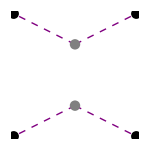
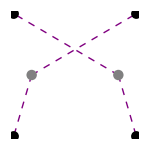
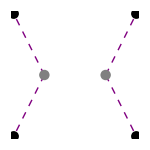
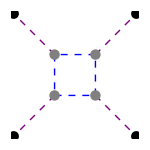
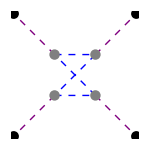
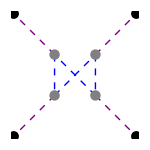

```mathematica
FourPtInvariantGraphs[GlobalRep/@Multiplet[1][[{1,1,1,1}]]]
```

```mathematica
AbsoluteTiming[corr=Correlator[NormalOrder[TensorProduct[QTensor[],Tensor[{"χ","J","J","J"}]],"Vacuum"->True]];]
```

{0.0486624,Null}

```mathematica
AbsoluteTiming[expr=ExpandCorrelator[corr];]
```

{747.277,Null}

```mathematica
rstructs=DeleteDuplicates[RPart/@(List@@Expand[expr])]
```

{C_l_28^(i_(8_v)i_(56_v))C_1^l_28i_28j_28k_28,C_l_28^(i_(8_v)i_(56_v))C_2^l_28i_28j_28k_28,C_l_28^(i_(8_v)i_(56_v))C_3^l_28i_28j_28k_28,C_l_28^(i_(8_v)i_(56_v))C_4^l_28i_28j_28k_28,C_l_28^(i_(8_v)i_(56_v))C_5^l_28i_28j_28k_28,C_l_28^(i_(8_v)i_(56_v))C_6^l_28i_28j_28k_28,C_l_28^(i_(8_v)i_(56_v))C_7^l_28i_28j_28k_28,(C_(i_(35_s)))^(i_(8_v)i_(56_v))C_1^(i_(35_s)i_28j_28k_28),(C_(i_(35_s)))^(i_(8_v)i_(56_v))C_2^(i_(35_s)i_28j_28k_28),(C_(i_(35_s)))^(i_(8_v)i_(56_v))C_3^(i_(35_s)i_28j_28k_28),(C_(i_(35_c)))^(i_(8_v)i_(56_v))C_1^(i_(35_c)i_28j_28k_28),(C_(i_(35_c)))^(i_(8_v)i_(56_v))C_2^(i_(35_c)i_28j_28k_28),(C_(i_(35_c)))^(i_(8_v)i_(56_v))C_3^(i_(35_c)i_28j_28k_28),(C_(j_(8_v)))^(i_(8_v)k_28)C_1^(i_(56_v)i_28j_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)j_28)C_1^(i_(56_v)i_28k_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)i_28)C_1^(i_(56_v)j_28k_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)k_28)C_2^(i_(56_v)i_28j_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)j_28)C_2^(i_(56_v)i_28k_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)i_28)C_2^(i_(56_v)j_28k_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)k_28)C_3^(i_(56_v)i_28j_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)j_28)C_3^(i_(56_v)i_28k_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)i_28)C_3^(i_(56_v)j_28k_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)k_28)C_4^(i_(56_v)i_28j_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)j_28)C_4^(i_(56_v)i_28k_28j_(8_v)),(C_(j_(8_v)))^(i_(8_v)i_28)C_4^(i_(56_v)j_28k_28j_(8_v)),(C_(j_(56_v)))^(i_(8_v)i_28)C_1^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_1^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_1^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_2^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_2^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_2^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_3^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_3^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_3^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_4^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_4^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_4^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_5^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_5^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_5^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_6^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_6^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_6^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_7^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_7^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_7^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_8^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_8^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_8^(i_(56_v)j_(56_v)i_28j_28),(C_(j_(56_v)))^(i_(8_v)i_28)C_9^(i_(56_v)j_(56_v)j_28k_28),(C_(j_(56_v)))^(i_(8_v)j_28)C_9^(i_(56_v)j_(56_v)i_28k_28),(C_(j_(56_v)))^(i_(8_v)k_28)C_9^(i_(56_v)j_(56_v)i_28j_28)}

```mathematica
SCWIGEE`Private`RRelations[rstructs];//AbsoluteTiming
```

{0.0001142,Null}

```mathematica
structsOrig=DeleteDuplicates[NonRPart/@(List@@Expand[expr])];
structs=SortBy[structsOrig,First@Cases[#,s_correlator:>{Length[s[[4]]],s[[5]],-s[[7]]},All]&];
```

```mathematica
formulas=ResourceFunction["MonitorProgress"][Table[Normal@Flatten[ConformalStructures`Private`fastEvalCOC[s,z,{uu,vv}]],{s,structs}]];
```

```mathematica
formulas=formulas/.{u->uu,v->vv};
```

```mathematica
mat[i_]:=ArrayFlatten[{{formulas/.{z->2,uu->safes[[i,1]],vv->safes[[i,2]]},formulas/.{z->3,uu->safes[[i,1]],vv->safes[[i,2]]}}}];
```

```mathematica
safes=ConformalStructures`Private`safeCrossRatios[None];
```

```mathematica
(indices=IndependentSet[N@comps,"Indices"->True];)//AbsoluteTiming
Length[indices]
```

{0.539985,Null}

432

```mathematica
DeleteFile["C:/users/rossd/documents/mat_formula.m"];
Save["C:/users/rossd/documents/mat_formula.m",{mat,formulas,safes,indices}];
```

```mathematica
comps=Flatten/@ResourceFunction["MonitorProgress"][Table[Flatten[ConformalStructures`Private`fastEvalCOC[s,z,safes[[11]]]],{s,structs},{z,2,3}]];
Dimensions[comps]
```

{1377,512}

```mathematica
Get["C:/users/rossd/MIT Dropbox/Ross Dempsey/Documents/ward/rels_fit.m"];
rels=Map[#/.{U->u[3,{1,2,3,4}],V->v[3,{1,2,3,4}]}&,fitmat,{2}];
```

```mathematica
sbzExpr=MinimalBy[rels,Length@*ArrayRules][[1]].structs;
```

```mathematica
sbzcomps=CanonicallyOrderedComponents[sbzExpr];
```

```mathematica
random=Thread[Flatten[Array[x,{4,3}]]->RandomInteger[10,12]]
```

{x_1^1→2,x_1^2→6,x_1^3→4,x_2^1→9,x_2^2→3,x_2^3→5,x_3^1→9,x_3^2→10,x_3^3→1,x_4^1→7,x_4^2→3,x_4^3→3}

```mathematica
ArrayRules[sbzcomps][[;;10]]/.random//Simplify
```

{{1,1,1,1,1,1,1,1}→0,{1,1,1,1,1,1,1,2}→0,{1,1,1,1,1,1,2,1}→0,{1,1,1,1,1,1,2,2}→0,{1,1,1,1,1,2,1,1}→0,{1,1,1,1,1,2,1,2}→0,{1,1,1,1,1,2,2,1}→0,{1,1,1,1,1,2,2,2}→0,{1,1,1,1,2,1,1,1}→0,{1,1,1,1,2,1,1,2}→0}

```mathematica
Transpose[comps[[%39[[2]],;;512]]]//Dimensions
Transpose[comps[[Complement[Range@Length[comps],%39[[2]]],;;512]]]//Dimensions
```

{512,432}

{512,945}

```mathematica
Length[%23[[2]]]
```

252

```mathematica
AbsoluteTiming[Table[Flatten[ConformalStructures`Private`fastEvalCOC[s,2,safes[[1]]]],{s,structs}];]
```

{171.324,Null}

```mathematica
StructureRelations[structs]
```

$Aborted

```mathematica
Flatten[CanonicallyOrderedComponents[rstructs[[1]]]]
Length[%]
```

SparseArray[…]

```mathematica
ExpansionComponents[expr]
```

$Aborted

```mathematica
structs=DeleteDuplicates[NonRPart/@(List@@Expand[expr])];
```

```mathematica
comps=ResourceFunction["MonitorProgress"][Table[Flatten[{Table[Normal[ConformalStructures`Private`fastEvalCOC[s,z,ConformalStructures`Private`safeCrossRatios[None][[11]]]],{z,2,5}]}],{s,structs}]];
```

```mathematica
AbsoluteTiming[IndependentSet[comps,"Indices"->True]]
```

{0.923092,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,70,71,72,73,76,94,97,100,103,106,109,112,115,118,121,124,127,130,133,136,139,142,145,148,151,154,157,160,163,211,214,217,220,223,226,229,232,235,238,241,244,247,250,253,256,259,262,265,268,271,274,277,280}}

```mathematica
?AllTrue
```

```mathematica
NumericQ[{3,4}]
```

False

```mathematica
data=ResourceFunction["MonitorProgress"][Table[Flatten[{Table[Normal[ConformalStructures`Private`fastEvalCOC[s,z,ConformalStructures`Private`safeCrossRatios[None][[11]]]],{z,2,5}]}],{s,structs}]];
```

```mathematica
MatrixRank[data]
```

432

```mathematica
Options[IndependentSet]={"TensorFunction"->CanonicallyOrderedComponents,"Rules"->{},"MaxIndependent"->Infinity,"Indices"->False};
IndependentSet[{}]:={};
IndependentSet[tensors_,OptionsPattern[]]:=If[!ArrayQ[OptionValue["TensorFunction"][tensors[[1]]]],If[TrueQ[OptionValue["Indices"]],{1},tensors[[{1}]]],With[{indices=Module[{runningComps=SparseArray[{},{Length[tensors],Length[Flatten[OptionValue["TensorFunction"][tensors[[1]]]]]}]},ResourceFunction["MonitorProgress"][Fold[If[Length[#1]<OptionValue["MaxIndependent"],With[{comp=Flatten@Normal@OptionValue["TensorFunction"][tensors[[#2]]]/. OptionValue["Rules"]},If[ConformalStructures`Private`indQ[runningComps[[;;Length[#1]]],comp],runningComps[[Length[#1]+1]]=comp;
Append[#1,#2],#1]],#1]&,{},Range@Length[tensors]],"CurrentDisplayFunction"->(Length[ToExpression["{"<>ToString[#]<>"}"][[1]]]&)]]},If[TrueQ[OptionValue["Indices"]],indices,tensors[[indices]]]]];
```

```mathematica
ExtractIndependentRowsFast[mat_]:=Module[{trans,reduced,indices},
trans=Transpose[mat];
reduced=RowReduce[trans];
indices=(Table[FirstPosition[row,x:Except[0]/;NumericQ[x]],{row,reduced}]/._?MissingQ->Nothing)[[;;,1]];
indices
]
```

```mathematica
ExtractIndependentRowsFast[N@data]//AbsoluteTiming
```

{0.908296,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,178,179,181,182,183,184,185,186,187,188,189,190,191,192,193,196,197,199,200,201,203,205,206,207,208,209,217,218,219,220,223,224,235,236,237,238,241,242,244,246,253,352,355,358,361,364,367,370,373,376,379,382,385,388,391,394,397,400,403,406,409,412,415,418,421,424,427,430,433,436,439,442,445,448,451,454,457,460,463,466,469,472,475,478,481,484,487,490,493,496,499,502,505,508,511,514,517,520,523,526,529,532,535,538,541,544,547,550,553,556,559,562,565,568,571,574,577,580,583,586,589,592,595,598,601,604,607,610,613,616,619,622,625,628,631,634,637,640,643,646,649,652,655,658,661,664,667,670,673,703,706,709,712,715,718,721,724,727,730,733,736,739,742,745,748,751,754,757,760,763,766,769,772,775,778,781,784,787,790,793,796,799,802,805,808,811,814,817,820,823,826,829,832,835,838,841,844,847,850,853,856,859,862,865,868,871,874,877,880,883,886,889,892,895,898,901,904,907,910,913,916,919,922,925,928,931,934,937,940,943,946,949,952,955,958,961,964,967,970,973,976,979,982,985,988,991,994,997,1000,1003,1006,1009,1012,1015,1018,1021,1024}}

```mathematica
MatrixRank[data[[%235[[2]]]]]
```

432

```mathematica
MatrixRank[data[[;;256]]]//AbsoluteTiming
```

{100.599,216}

```mathematica
Length[%228[[2]]]
```

216

### Find

```mathematica
eqs=WardEquations[{"S","S","S","χ"},"UseSUSYRules"->False];
```

```mathematica
Format[𝒮[i_],TraditionalForm]:=Subscript[𝒮,i];
```

```mathematica
DeclareArbitraryFunction/@Array[𝒮,6];
trial=Table[g[Multiplet[1][[{1,1,1,1}]],i,1]->({u,v}|->Evaluate[𝒮[i][u,v]]),{i,6}]
```

{g_(1,1)^SSSS→({u,v}↦𝒮_1(u,v)),g_(2,1)^SSSS→({u,v}↦𝒮_2(u,v)),g_(3,1)^SSSS→({u,v}↦𝒮_3(u,v)),g_(4,1)^SSSS→({u,v}↦𝒮_4(u,v)),g_(5,1)^SSSS→({u,v}↦𝒮_5(u,v)),g_(6,1)^SSSS→({u,v}↦𝒮_6(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[ops_,__][__],All];
```

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
nulls=Simplify@NullSpace[Transpose[Normal[mm]]];
```

```mathematica
sbz=Simplify[nulls.(Normal[bb])];
```

```mathematica
fvars=DeleteDuplicates@Cases[sbz,Derivative[__][𝒮[i_]][__]/;i>3,All]
```

{𝒮_4^(0,1)(u,v),𝒮_5^(0,1)(u,v),𝒮_6^(0,1)(u,v),𝒮_4^(1,0)(u,v),𝒮_5^(1,0)(u,v),𝒮_6^(1,0)(u,v)}

```mathematica
Ssol=Simplify@First@Solve[Thread[sbz==0],fvars]
AddSolutions[Ssol]
```

{𝒮_4^(0,1)(u,v)→1/16 (-(𝒮_3(u,v))/u-(8 𝒮_4(u,v)+(u+v-1) 𝒮_1^(0,1)(u,v)+u 𝒮_1^(1,0)(u,v)-v 𝒮_3^(1,0)(u,v))/v),𝒮_5^(0,1)(u,v)→(𝒮_2(u,v)+u ((v-1) 𝒮_1^(0,1)(u,v)-𝒮_2^(0,1)(u,v)+u 𝒮_1^(1,0)(u,v)-𝒮_2^(1,0)(u,v)))/(16 u),𝒮_6^(0,1)(u,v)→-(v^2 𝒮_3^(0,1)(u,v)+u v 𝒮_3^(1,0)(u,v)+𝒮_2(u,v)+8 𝒮_6(u,v)-u 𝒮_2^(0,1)(u,v)+𝒮_2^(0,1)(u,v)-u 𝒮_2^(1,0)(u,v))/(16 v),𝒮_4^(1,0)(u,v)→((v-1) 𝒮_3(u,v)+u (8 𝒮_4(u,v)+u 𝒮_1^(0,1)(u,v)-v 𝒮_3^(0,1)(u,v)-u 𝒮_3^(1,0)(u,v)-v 𝒮_3^(1,0)(u,v)+𝒮_3^(1,0)(u,v)))/(16 u^2),𝒮_5^(1,0)(u,v)→-(u (u^2 𝒮_1^(1,0)(u,v)+u v 𝒮_1^(0,1)(u,v)-8 𝒮_5(u,v)-v 𝒮_2^(0,1)(u,v)-v 𝒮_2^(1,0)(u,v)+𝒮_2^(1,0)(u,v))+(v-1) 𝒮_2(u,v))/(16 u^2),𝒮_6^(1,0)(u,v)→(u^2 𝒮_3^(1,0)(u,v)-u 𝒮_2^(0,1)(u,v)+u v 𝒮_3^(0,1)(u,v)-u 𝒮_2^(1,0)(u,v)-u 𝒮_3^(1,0)(u,v)+𝒮_2(u,v)+𝒮_3(u,v)+16 𝒮_6(u,v))/(16 u)}

```mathematica
Svars[n_]:=Svars[n]=Flatten@Table[Derivative[i,j][𝒮[k]][u,v],{k,6},{i,0,If[k<=3,n,0]},{j,0,If[k<=3,n-i,0]}]
```

```mathematica
twoderivRels=Table[D[Ssol[[i,2]],u]-D[Ssol[[i+3,2]],v],{i,3}]/.Normal[First/@SolvedCorrelators[]];
twoderivM=CoefficientArrays[twoderivRels,Svars[2]][[2]];
MatrixRank[twoderivM]
twoderivSol=Simplify@First@Solve[Simplify@Thread[twoderivM.Svars[2]==0],{Derivative[2,0][𝒮[2]][u,v],Derivative[2,0][𝒮[3]][u,v]}];
twoderivs=Join[Map[D[#,u]&,Normal[KeyMap[#[u,v]&,#[u,v]&/@First/@SolvedCorrelators[]]],{2}],Map[D[#,v]&,Normal[KeyMap[#[u,v]&,#[u,v]&/@First/@SolvedCorrelators[]]],{2}]]//.Join[Normal[First/@SolvedCorrelators[]],twoderivSol]//Simplify;
AddSolutions[Join[twoderivs,twoderivSol]];
```

2

```mathematica
threederivRels=Join[Table[D[Ssol[[i,2]],u,v]-D[Ssol[[i+3,2]],{v,2}],{i,3}],Table[D[Ssol[[i,2]],{u,2}]-D[Ssol[[i+3,2]],u,v],{i,3}]]/.Normal[First/@SolvedCorrelators[]]//Simplify;
threederivM=CoefficientArrays[threederivRels,Svars[3]][[2]];
MatrixRank[threederivM]
threederivSol=Simplify@First@Solve[Simplify@Thread[threederivM.Svars[3]==0],{Derivative[2,1][𝒮[2]][u,v],Derivative[2,1][𝒮[3]][u,v],Derivative[3,0][𝒮[2]][u,v],Derivative[3,0][𝒮[3]][u,v]}];
threederivs=DeleteCases[Select[Join[Map[D[#,u]&,Normal[KeyMap[#[u,v]&,#[u,v]&/@First/@SolvedCorrelators[]]],{2}],Map[D[#,v]&,Normal[KeyMap[#[u,v]&,#[u,v]&/@First/@SolvedCorrelators[]]],{2}]],Total[List@@#[[1,0,0]]]==3&]//.Join[Normal[First/@SolvedCorrelators[]],threederivSol]//Simplify,HoldPattern[x_->x_]];
AddSolutions[Join[threederivs,threederivSol]];
```

4

```mathematica
fourderivRels=Join[Table[D[Ssol[[i,2]],u,{v,2}]-D[Ssol[[i+3,2]],{v,3}],{i,3}],Table[D[Ssol[[i,2]],{u,2},v]-D[Ssol[[i+3,2]],u,{v,2}],{i,3}],Table[D[Ssol[[i,2]],{u,3}]-D[Ssol[[i+3,2]],{u,2},v],{i,3}]]/.Normal[First/@SolvedCorrelators[]]//Simplify;
fourderivM=CoefficientArrays[fourderivRels,Svars[4]][[2]];
MatrixRank[fourderivM]
fourderivSol=Simplify@First@Solve[Simplify@Thread[fourderivM.Svars[4]==0],{Derivative[2,2][𝒮[2]][u,v],Derivative[2,2][𝒮[3]][u,v],Derivative[3,1][𝒮[2]][u,v],Derivative[3,1][𝒮[3]][u,v],Derivative[4,0][𝒮[2]][u,v],Derivative[4,0][𝒮[3]][u,v]}];
fourderivs=DeleteCases[Select[Join[Map[D[#,u]&,Normal[KeyMap[#[u,v]&,#[u,v]&/@First/@SolvedCorrelators[]]],{2}],Map[D[#,v]&,Normal[KeyMap[#[u,v]&,#[u,v]&/@First/@SolvedCorrelators[]]],{2}]],Total[List@@#[[1,0,0]]]==4&]//.Join[Normal[First/@SolvedCorrelators[]],fourderivSol]//Simplify,HoldPattern[x_->x_]];
AddSolutions[Join[fourderivs,fourderivSol]];
```

6

### Solve identities

```mathematica
AddSolutions[#[[1]][u,v]->#[[2]][u,v]&/@trial];
```

```mathematica
DeclareCrossingRule@@@CrossingRelations[Multiplet[1][[{1,1,1,1}]]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","S","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","χ","J"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","χ","J","J"}]];
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"S","S","χ","P"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","χ","P","P"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","P","P","P"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","χ","J"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","χ","P","J"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","P","P","J"}]];
```

```mathematica
eqs=WardEquations[{"S","χ","J","J"}];
```

```mathematica
eqssubbed=ResourceFunction["MonitorProgress"]@Table[SCWIGEE`Private`swSimplify[CrossingSimplify[SCWIGEE`Private`swSimplify[eqs[[i]]//.Normal[First/@SolvedCorrelators[]]]]//.Normal[First/@SolvedCorrelators[]]],{i,Length[eqs]}];
```

$Aborted

## 𝒩 = 2 Interface

```mathematica
SetSpacetimeDimension[4];
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[U1,{{1,0}}];
SetSignature["Euclidean"];
SetDefectCodimension[1];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"K\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"K\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
alleqs=Join[WardEquations[{"J","ξ"},"Defect"->True],WardEquations[{"J","ξ̄"},"Defect"->True]];
vars=DeleteDuplicates@Cases[alleqs,g[fields_,__][__]/;Total[ScalingDimension/@fields]>4,All];
{bb,mm}=Normal[CoefficientArrays[alleqs,vars]];
(consistency=NullSpace[Transpose[mm]].bb//Simplify);
scpVars=Reverse@DeleteDuplicates[Cases[consistency,Derivative[__][g[x__]][y__]:>g[x][y],All]];
consistencySol=Simplify@First@Solve[Thread[consistency==0],{D[scpVars[[1]],u]}]
```

{g_(1,1)^J_0J_0'(u)→(2 u+1) g_(1,1)^(J_-2J_2)'(u)+4 g_(1,1)^(J_-2J_2)(u)}

```mathematica
AddSolutions[consistencySol]
```

```mathematica
AddSolutions[SolveWard[{"J","ξ"},"Defect"->True]];
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True]];
```

```mathematica
AddSolutions[SolveWard[{"ξ","K"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ","K̄"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ̄","K"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ̄","K̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","j"},"Defect"->True]]
AddSolutions[SolveWard[{"ξ̄","j"},"Defect"->True]]
```

```mathematica
Normal[SolvedCorrelators[]]//TableForm
```

g_(1,1)^J_0J_0'→{{u}↦(2 u+1) g_(1,1)^(J_-2J_2)'(u)+4 g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^J_0j_0→{{u}↦0}
g_(1,1)^J_0K_0→{{u}↦1/2 g_(1,1)^J_0J_0(u)+1/2 u (u+1) g_(1,1)^(J_-2J_2)'(u)+(u+1/2) g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^(ξ_-1(ξ̄)_1)→{{u}↦-1/8 ⅈ (u+1) g_(1,1)^(J_-2J_2)'(u)-1/4 ⅈ g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^(ξ_-1ξ_1)→{{u}↦1/8 ⅈ u g_(1,1)^(J_-2J_2)'(u)+1/4 ⅈ g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^(ξ_1(ξ̄)_-1)→{{u}↦-1/8 ⅈ (u+1) g_(1,1)^(J_-2J_2)'(u)-1/4 ⅈ g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^(J_0(K̄)_0)→{{u}↦-1/2 g_(1,1)^J_0J_0(u)-1/2 u (u+1) g_(1,1)^(J_-2J_2)'(u)+(-u-1/2) g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^((ξ̄)_-1(ξ̄)_1)→{{u}↦-1/8 ⅈ u g_(1,1)^(J_-2J_2)'(u)-1/4 ⅈ g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^j_0K_0→{{u}↦0}
g_(1,1)^K_0K_0→{{u}↦-1/4 g_(1,1)^J_0J_0(u)-1/8 u ((8 u+6) g_(1,1)^(J_-2J_2)'(u)+u (u+1) g_(1,1)^(J_-2J_2)''(u))+1/4 (-5 u-2) g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^(j_0(K̄)_0)→{{u}↦0}
g_(1,1)^(K_0(K̄)_0)→{{u}↦1/4 g_(1,1)^J_0J_0(u)+1/8 (u+1) ((8 u+2) g_(1,1)^(J_-2J_2)'(u)+u (u+1) g_(1,1)^(J_-2J_2)''(u))+1/4 (5 u+3) g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^((K̄)_0(K̄)_0)→{{u}↦-1/4 g_(1,1)^J_0J_0(u)-1/8 u ((8 u+6) g_(1,1)^(J_-2J_2)'(u)+u (u+1) g_(1,1)^(J_-2J_2)''(u))+1/4 (-5 u-2) g_(1,1)^(J_-2J_2)(u)}
g_(1,1)^j_0j_0→{{u}↦1/96 (-3 g_(1,1)^(J_-2J_2)'(u)-u g_(1,1)^(J_-2J_2)''(u))}
g_(1,2)^j_0j_0→{{u}↦1/96 (3 g_(1,1)^(J_-2J_2)'(u)+(u+1) g_(1,1)^(J_-2J_2)''(u))}

```mathematica
Normal[SolvedCorrelators[]][[2;;]]/.HoldPattern[key_->value_]:>(key->value[[1]][u])/.g[{Multiplet[1][[1]]/.{{2},0}->-2,Multiplet[1][[1]]/.{{2},0}->2},1,1]->({u}|->1/(16 u^2))/.g[{Multiplet[1][[1]]/.{{2},0}->0,Multiplet[1][[1]]/.{{2},0}->0},1,1]->({u}|->1/(16 u^2))//FullSimplify
```

{g_(1,1)^J_0j_0→0,g_(1,1)^J_0K_0→0,g_(1,1)^(ξ_-1(ξ̄)_1)→ⅈ/(64 u^3),g_(1,1)^(ξ_-1ξ_1)→0,g_(1,1)^(ξ_1(ξ̄)_-1)→ⅈ/(64 u^3),g_(1,1)^(J_0(K̄)_0)→0,g_(1,1)^((ξ̄)_-1(ξ̄)_1)→0,g_(1,1)^j_0K_0→0,g_(1,1)^K_0K_0→0,g_(1,1)^(j_0(K̄)_0)→0,g_(1,1)^(K_0(K̄)_0)→1/(64 u^3),g_(1,1)^((K̄)_0(K̄)_0)→0,g_(1,1)^j_0j_0→0,g_(1,2)^j_0j_0→1/(256 u^4)}

## 𝒩 = 2 (4,0) Surface Defect

```mathematica
SetSpacetimeDimension[4];
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[SU2];
SetSignature["Euclidean"];
SetDefectCodimension[2,{4,0}];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"K\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"K\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->False]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->False]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K̄","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","j"},"Defect"->True,"QBar"->True]];
AddSolutions[SolveWard[{"j","ξ̄"},"Defect"->True]];
```

```mathematica
(v-I √(1-v^2))^2//Expand
```

2 v^2-2 ⅈ √(1-v^2) v-1

```mathematica
SCWIGEE`Private`swSimplify[8(v-I √(1-v^2))SolvedCorrelators[][[7,1]][u,v],1>v>0]
```

((√(1-v^2)+ⅈ v) (2 v^2+ⅈ √(1-v^2) v-2) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(ⅈ v^2+√(1-v^2) v-ⅈ)+(1-v^2) (g_(1,1)^J_3J_3)^(0,2)(u,v)+(3 u+ⅈ √(1-v^2)+2 v) (g_(1,1)^J_3J_3)^(1,0)(u,v)+(v^2-1) (g_(1,1)^J_3J_3)^(1,1)(u,v)+u (u+v) (g_(1,1)^J_3J_3)^(2,0)(u,v)

```mathematica
Normal[SolvedCorrelators[]]//TableForm
```

g_(1,1)^(ξ_2(ξ̄)_2)→{{u,v}↦(g_(1,1)^J_3J_3(u,v))/(4 √(1-v^2)+4 ⅈ v)+(ⅈ √(1-v^2) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(8 √(1-v^2)+8 ⅈ v)+((u-ⅈ √(1-v^2)+v) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(8 √(1-v^2)+8 ⅈ v)}
g_(1,2)^(ξ_2(ξ̄)_2)→{{u,v}↦(ⅈ g_(1,1)^J_3J_3(u,v))/(4 (√(1-v^2)+ⅈ v))-(√(1-v^2) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(8 (√(1-v^2)+ⅈ v))+(ⅈ u (g_(1,1)^J_3J_3)^(1,0)(u,v))/(8 (√(1-v^2)+ⅈ v))}
g_(1,1)^ξ_2ξ_2→{{u,v}↦0}
g_(1,2)^ξ_2ξ_2→{{u,v}↦0}
g_(1,1)^((ξ̄)_2(ξ̄)_2)→{{u,v}↦0}
g_(1,2)^((ξ̄)_2(ξ̄)_2)→{{u,v}↦0}
g_(1,1)^(K_1(K̄)_1)→{{u,v}↦((-2 ⅈ v^2+√(1-v^2) v+2 ⅈ) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(-8 ⅈ v^2-8 √(1-v^2) v+8 ⅈ)-(ⅈ (v^2-1) (g_(1,1)^J_3J_3)^(0,2)(u,v))/(8 (√(1-v^2)+ⅈ v))+((3 ⅈ u-√(1-v^2)+2 ⅈ v) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(8 √(1-v^2)+8 ⅈ v)+(ⅈ (v^2-1) (g_(1,1)^J_3J_3)^(1,1)(u,v))/(8 (√(1-v^2)+ⅈ v))+(ⅈ u (u+v) (g_(1,1)^J_3J_3)^(2,0)(u,v))/(8 (√(1-v^2)+ⅈ v))}
g_(1,1)^((K̄)_1(K̄)_1)→{{u,v}↦0}
g_(1,1)^K_1K_1→{{u,v}↦0}
g_(1,1)^j_1j_1→{{u,v}↦(√(1-v^2) (4 ⅈ v^3-4 √(1-v^2) v^2+√(1-v^2)-3 ⅈ v) (-2 u^2-3 u v-1) (g_(1,1)^J_3J_3)^(2,0)(u,v))/(96 (-4 v^4+5 v^2+3 ⅈ √(1-v^2) v-4 ⅈ √(1-v^2) v^3-1))+1/48 (1-v^2) (g_(1,1)^J_3J_3)^(0,2)(u,v)+1/32 (v^2-1) (g_(1,1)^J_3J_3)^(1,1)(u,v)+(√(1-v^2) (4 ⅈ v^3-4 √(1-v^2) v^2+√(1-v^2)-3 ⅈ v) (-10 u-9 v) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(96 (-4 v^4+5 v^2+3 ⅈ √(1-v^2) v-4 ⅈ √(1-v^2) v^3-1))+1/12 g_(1,1)^J_3J_3(u,v)-1/48 v (g_(1,1)^J_3J_3)^(0,1)(u,v)}
g_(1,2)^j_1j_1→{{u,v}↦((16 ⅈ v^6-16 √(1-v^2) v^5-12 ⅈ v^4+4 √(1-v^2) v^3-3 ⅈ v^2+3 √(1-v^2) v-2 u (-16 ⅈ v^5+16 √(1-v^2) v^4+20 ⅈ v^3-12 √(1-v^2) v^2-5 ⅈ v+√(1-v^2))+ⅈ) (g_(1,1)^J_3J_3)^(0,2)(u,v) (v^2-1)^2)/(96 (u+v) (√(1-v^2)-ⅈ v)^2 (-ⅈ v^2+√(1-v^2) v+ⅈ) (-2 ⅈ v^3+2 √(1-v^2) v^2+2 ⅈ v-√(1-v^2)))-(√(1-v^2) (-4 ⅈ v^4+4 √(1-v^2) v^3+ⅈ v^2+√(1-v^2) v+u (-8 ⅈ v^3+8 √(1-v^2) v^2+6 ⅈ v-2 √(1-v^2))+ⅈ) g_(1,1)^J_3J_3(u,v))/(24 (u+v) (√(1-v^2)-ⅈ v)^2 (-ⅈ v^2+√(1-v^2) v+ⅈ))+(v √(1-v^2) (-4 ⅈ v^4+4 √(1-v^2) v^3+ⅈ v^2+√(1-v^2) v+u (-8 ⅈ v^3+8 √(1-v^2) v^2+6 ⅈ v-2 √(1-v^2))+ⅈ) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(96 (u+v) (√(1-v^2)-ⅈ v)^2 (-ⅈ v^2+√(1-v^2) v+ⅈ))+(√(1-v^2) (5 (16 v^5+16 ⅈ √(1-v^2) v^4-20 v^3-12 ⅈ √(1-v^2) v^2+5 v+ⅈ √(1-v^2)) u^2+4 (16 v^6+16 ⅈ √(1-v^2) v^5-12 v^4-4 ⅈ √(1-v^2) v^3-3 v^2-3 ⅈ √(1-v^2) v+1) u+3 v (8 v^4+8 ⅈ √(1-v^2) v^3-8 v^2-4 ⅈ √(1-v^2) v+1)) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(48 (u+v) (-v^2-ⅈ √(1-v^2) v+1) (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ)^2)-(√(1-v^2) (4 v^4+4 ⅈ √(1-v^2) v^3-5 v^2-3 ⅈ √(1-v^2) v+u (-16 v^7-16 ⅈ √(1-v^2) v^6+44 v^5+36 ⅈ √(1-v^2) v^4-37 v^3-21 ⅈ √(1-v^2) v^2+9 v+2 ⅈ √(1-v^2))+1) (g_(1,1)^J_3J_3)^(1,1)(u,v))/(96 (u+v) (-v^2-ⅈ √(1-v^2) v+1) (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ)^2)+(u √(1-v^2) (8 v^4+8 ⅈ √(1-v^2) v^3-8 v^2-4 ⅈ √(1-v^2) v+u (16 v^5+16 ⅈ √(1-v^2) v^4-20 v^3-12 ⅈ √(1-v^2) v^2+5 v+ⅈ √(1-v^2))+1) (g_(1,1)^J_3J_3)^(2,0)(u,v))/(48 (-v^2-ⅈ √(1-v^2) v+1) (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ)^2)}
g_(1,3)^j_1j_1→{{u,v}↦((2 ⅈ v^2-2 √(1-v^2) v-ⅈ) (1-v^2)^(3/2) (g_(1,1)^J_3J_3)^(0,2)(u,v))/(48 (-2 ⅈ v^3+2 √(1-v^2) v^2-√(1-v^2)+2 ⅈ v))+((6 v^4-8 v^2-5 ⅈ √(1-v^2) v+6 ⅈ √(1-v^2) v^3+2) (g_(1,1)^J_3J_3)^(1,1)(u,v))/(96 (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ))+((10 u (-2 ⅈ v^3+2 √(1-v^2) v^2-√(1-v^2)+2 ⅈ v)+3 (-6 ⅈ v^4+7 ⅈ v^2-4 √(1-v^2) v+6 √(1-v^2) v^3-ⅈ)) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(96 (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ) √(1-v^2))+(u (u (-4 ⅈ v^3+4 √(1-v^2) v^2-2 √(1-v^2)+4 ⅈ v)-6 ⅈ v^4+7 ⅈ v^2-4 √(1-v^2) v+6 √(1-v^2) v^3-ⅈ) (g_(1,1)^J_3J_3)^(2,0)(u,v))/(96 (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ) √(1-v^2))+1/12 ⅈ g_(1,1)^J_3J_3(u,v)-1/48 ⅈ v (g_(1,1)^J_3J_3)^(0,1)(u,v)}
g_(1,4)^j_1j_1→{{u,v}↦(u^2 (-2 ⅈ v^2+(2 v)/(√(1-v^2))-(2 v^3)/(√(1-v^2))+ⅈ) (g_(1,1)^J_3J_3)^(2,0)(u,v))/(48 (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ))+(u (v^2-1) (g_(1,1)^J_3J_3)^(1,1)(u,v))/(96 (u+v))-((v^2-1) (2 u+v) (g_(1,1)^J_3J_3)^(0,2)(u,v))/(96 (u+v))+(u (-2 v^3-2 ⅈ √(1-v^2) v^2+ⅈ √(1-v^2)+2 v) (5 u+4 v) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(48 √(1-v^2) (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ) (u+v))+((2 u+v) g_(1,1)^J_3J_3(u,v))/(24 (u+v))-(v (2 u+v) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(96 (u+v))}
g_(1,5)^j_1j_1→{{u,v}↦0}
g_(1,6)^j_1j_1→{{u,v}↦((4 v^3+4 ⅈ √(1-v^2) v^2-ⅈ √(1-v^2)-3 v) (v^2-1)^2 (g_(1,1)^J_3J_3)^(0,2)(u,v))/(96 (-ⅈ v^2+√(1-v^2) v+ⅈ) (-2 ⅈ v^3+2 √(1-v^2) v^2-√(1-v^2)+2 ⅈ v) (u+v))-(√(1-v^2) (4 ⅈ v^3-4 √(1-v^2) v^2+√(1-v^2)-3 ⅈ v) (5 u+3 v) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(96 (-ⅈ v^2+√(1-v^2) v+ⅈ) (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ) (u+v))+((1-v^2)^(3/2) (4 ⅈ v^3-4 √(1-v^2) v^2+√(1-v^2)-3 ⅈ v) (g_(1,1)^J_3J_3)^(1,1)(u,v))/(96 (-ⅈ v^2+√(1-v^2) v+ⅈ) (-2 ⅈ v^2+2 √(1-v^2) v+ⅈ) (u+v))+(g_(1,1)^J_3J_3(u,v))/(24 (u+v))-(v (g_(1,1)^J_3J_3)^(0,1)(u,v))/(96 (u+v))+1/96 u (g_(1,1)^J_3J_3)^(2,0)(u,v)}

```mathematica
Normal[SolvedCorrelators[]]/.HoldPattern[key_->value_]:>(key->value[[1]][u,v])/.g[Multiplet[1][[{1,1}]]/.{{2},0}->{2},1,1]->({u,v}|->1/(16 u^2))//FullSimplify
```

{g_(1,1)^(ξ_2(ξ̄)_2)→ⅈ/(64 u^3),g_(1,2)^(ξ_2(ξ̄)_2)→0,g_(1,1)^ξ_2ξ_2→0,g_(1,2)^ξ_2ξ_2→0,g_(1,1)^((ξ̄)_2(ξ̄)_2)→0,g_(1,2)^((ξ̄)_2(ξ̄)_2)→0,g_(1,1)^(K_1(K̄)_1)→1/(64 u^3),g_(1,1)^((K̄)_1(K̄)_1)→0,g_(1,1)^K_1K_1→0,g_(1,1)^j_1j_1→1/(256 u^4),g_(1,2)^j_1j_1→0,g_(1,3)^j_1j_1→0,g_(1,4)^j_1j_1→0,g_(1,5)^j_1j_1→0,g_(1,6)^j_1j_1→0}

### Check N=(4,0) defect

```mathematica
mine=SolvedCorrelators[][[7,1]][u,v]
```

((-2 ⅈ v^2+√(1-v^2) v+2 ⅈ) (g_(1,1)^J_3J_3)^(0,1)(u,v))/(-8 ⅈ v^2-8 √(1-v^2) v+8 ⅈ)-(ⅈ (v^2-1) (g_(1,1)^J_3J_3)^(0,2)(u,v))/(8 (√(1-v^2)+ⅈ v))+((3 ⅈ u-√(1-v^2)+2 ⅈ v) (g_(1,1)^J_3J_3)^(1,0)(u,v))/(8 √(1-v^2)+8 ⅈ v)+(ⅈ (v^2-1) (g_(1,1)^J_3J_3)^(1,1)(u,v))/(8 (√(1-v^2)+ⅈ v))+(ⅈ u (u+v) (g_(1,1)^J_3J_3)^(2,0)(u,v))/(8 (√(1-v^2)+ⅈ v))

```mathematica
rules=First@Quiet@Solve[Cosh[ρ]==2u+v&&Exp[I θ]==v+I √(1-v^2),{u,v}]
```

{u→1/4 (-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)+2 cosh(ρ)),v→1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))}

```mathematica
Sinh[ρ]^-2 D[Sinh[ρ]^2 D[Exp[I θ]f[u,v]/.rules,ρ],ρ]+D[Exp[I θ]f[u,v]/.rules,{θ,2}]+Exp[I θ]f[u,v]/.rules
silviu=Simplify[%]/.{ρ->ArcCosh[2u+v],θ->-I Log[v+I √(1-v^2)]}//FullSimplify
```

(1/4 ⅇ^(ⅈ θ) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^4(ρ)+3/2 ⅇ^(ⅈ θ) cosh(ρ) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^2(ρ)) csch^2(ρ)+2 ⅈ ⅇ^(ⅈ θ) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+ⅇ^(ⅈ θ) (-1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+(ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,2)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))))

(-3 v^2-3 ⅈ √(1-v^2) v+2) f^(0,1)(u,v)-ⅈ (√(1-v^2)-ⅈ v) ((v^2-1) f^(0,2)(u,v)-(v^2-1) f^(1,1)(u,v)-3 (u+v) f^(1,0)(u,v)-u (u+v) f^(2,0)(u,v))-f^(1,0)(u,v)

```mathematica
Simplify[8 mine-silviu/.g[__]->f]
```

0

## 𝒩 = 2 (2,2) Surface Defect

```mathematica
SetSpacetimeDimension[4];
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[U1,{{1,0}}];
SetSignature["Euclidean"];
SetDefectCodimension[2,{2,2}];
```

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"j\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"K\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"K\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Automated Ward identities and solutions

```mathematica
eqs=Join[WardEquations[{"J","ξ̄"},"Defect"->True,"QBar"->False],WardEquations[{"ξ","J"},"Defect"->True,"QBar"->True]];
vars=DeleteDuplicates[Cases[eqs,g[fields_,__][__]/;Total[ScalingDimension/@fields]>4,All]];
```

```mathematica
{bb,mm}=Normal[CoefficientArrays[eqs,vars]];
```

```mathematica
consistency=NullSpace[Transpose[mm]].bb//Simplify;
```

```mathematica
jjs=DeleteDuplicates@Cases[consistency,Derivative[__][g[__]][__],All];
sol=First@Solve[Thread[consistency==0],jjs]
AddSolutions[sol];
```

{(g_(1,1)^J_0J_0)^(1,0)(u,v)→(g_(1,1)^(J_-2J_2))^(1,0)(u,v),(g_(1,1)^J_0J_0)^(0,1)(u,v)→(g_(1,1)^(J_-2J_2))^(0,1)(u,v)-(2 ⅈ (g_(1,1)^(J_-2J_2)(u,v)-g_(1,1)^J_0J_0(u,v)))/(√(1-v^2))}

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->False]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","J"},"Defect"->True,"QBar"->False]]
AddSolutions[SolveWard[{"J","ξ̄"},"Defect"->True,"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"K̄","ξ̄"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"ξ","K"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"ξ","j"},"Defect"->True,"QBar"->True]];
```

```mathematica
Normal[SolvedCorrelators[]][[3;;]]/.HoldPattern[key_->value_]:>(key->value[[1]][u,v])/.g[fields_,1,1]/;Total[ScalingDimension/@fields]==4->({u,v}|->1/(16 u^2))//FullSimplify
```

{g_(1,1)^J_0j_0→0,g_(1,2)^J_0j_0→0,g_(1,1)^(ξ_-1(ξ̄)_1)→ⅈ/(64 u^3),g_(1,2)^(ξ_-1(ξ̄)_1)→0,g_(1,1)^(ξ_1(ξ̄)_-1)→ⅈ/(64 u^3),g_(1,2)^(ξ_1(ξ̄)_-1)→0,g_(1,1)^J_0K_0→0,g_(1,1)^(ξ_-1ξ_1)→0,g_(1,2)^(ξ_-1ξ_1)→0,g_(1,1)^(J_0(K̄)_0)→0,g_(1,1)^((ξ̄)_-1(ξ̄)_1)→0,g_(1,2)^((ξ̄)_-1(ξ̄)_1)→0,g_(1,1)^(K_0(K̄)_0)→1/(64 u^3),g_(1,1)^((K̄)_0(K̄)_0)→0,g_(1,1)^K_0K_0→0,g_(1,1)^j_0j_0→0,g_(1,2)^j_0j_0→0,g_(1,3)^j_0j_0→0,g_(1,4)^j_0j_0→0,g_(1,5)^j_0j_0→1/(256 u^4),g_(1,6)^j_0j_0→0}

### Check JJ relation

```mathematica
rules=FullSimplify[FullSimplify[First@Quiet@Solve[u==(√((z-1)(zb-1)))/(4 √(z zb))&&v==(z+zb)/(2 √(z zb)),{z,zb}],0<u<1/4&&0<v<1&&16 u^2+v^2-1>0]/.√(-1+8 u^2+v^2-√((-1+v^2) (-1+16 u^2+v^2))) ->(√(16 u^2+v^2-1)-√(v^2-1))/(√2),0<u<1/4&&0<v<1&&16 u^2+v^2-1>0]
rules2={u->(√((z-1)(zb-1)))/(4 √(z zb)),v->(z+zb)/(2 √(z zb))};
```

{z→1/(v (√(16 u^2+v^2-1)-√(v^2-1)+v)-√((v^2-1) (16 u^2+v^2-1))),zb→-(-v (√(16 u^2+v^2-1)+√(v^2-1))+√((v^2-1) (16 u^2+v^2-1))+v^2)/(16 u^2-1)}

```mathematica
PowerExpand@FullSimplify[v/.rules2/.rules,0<u<1/4&&0<v<1&&16 u^2+v^2-1>0]
```

(v (v-√(v^2-1)) √(2 v (√(16 u^2+v^2-1)+v)+16 u^2-1))/(v (√(16 u^2+v^2-1)-√(v^2-1)+v)-√(v^2-1) √(16 u^2+v^2-1))

```mathematica
mat=Simplify@With[{vs=Normalize/@Eigenvectors[PauliMatrix[2]]},
α(j[-2] Outer[Times,vs[[1]],Conjugate[vs[[2]]]]+j[2]Outer[Times,vs[[2]],Conjugate[vs[[1]]]])+β j[0](Outer[Times,vs[[1]],Conjugate[vs[[1]]]]+Outer[Times,vs[[2]],Conjugate[vs[[2]]]])
]
```

(β j(0)-1/2 α (j(-2)+j(2)) | 1/2 ⅈ α (j(-2)-j(2))
1/2 ⅈ α (j(-2)-j(2)) | 1/2 α (j(-2)+j(2))+β j(0))

```mathematica
jsol=First@Solve[j[1,1]==mat[[1,1]]&&j[1,2]==mat[[1,2]]&&j[2,2]==mat[[2,2]],{j[-2],j[0],j[2]}]//Simplify
```

{j(-2)→-(j(1,1)+2 ⅈ j(1,2)-j(2,2))/(2 α),j(0)→(j(1,1)+j(2,2))/(2 β),j(2)→(-j(1,1)+2 ⅈ j(1,2)+j(2,2))/(2 α)}

```mathematica
corr[j[i_,j_],j[k_,l_]]:=(-ϵ[i,k]ϵ[l,j]-ϵ[i,l]ϵ[k,j])a1+(δ[i,k]δ[l,j]+δ[i,l]δ[k,j])a2/.δ[a_,b_]:>Boole[a==b]/.ϵ[a_,b_]:>Signature[{a,b}];
corr[a_+b_,c_]:=corr[a,c]+corr[b,c];
corr[a_,b_+c_]:=corr[a,b]+corr[a,c];
corr[a_ b_,c_]/;FreeQ[a,j]:=a corr[b,c];
corr[a_,b_ c_]/;FreeQ[b,j]:=b corr[a,c];

corr[j[0]/.jsol,j[0]/.jsol]//Simplify
corr[j[2]/.jsol,j[-2]/.jsol]//Simplify
```

(a1+a2)/β^2

-(2 (a1-a2))/α^2

```mathematica
stRules=Thread[DeleteDuplicates@Cases[sol[[2]],g[__],All,Heads->True]->{Function[{u,v},A1[u,v]+ A2[u,v]],Function[{u,v},A1[u,v]-A2[u,v]]}]
```

{g_(1,1)^J_0J_0→({u,v}↦A1(u,v)+A2(u,v)),g_(1,1)^(J_-2J_2)→({u,v}↦A1(u,v)-A2(u,v))}

```mathematica
constraints=Table[Simplify[(Equal@@s)/.stRules],{s,sol}]
```

{A2^(1,0)(u,v)==0,A2^(0,1)(u,v)-(2 ⅈ A2(u,v))/(√(1-v^2))==0}

```mathematica
zzbconstrs=FullSimplify[constraints/.{A1->Function[{u,v},Evaluate[A1[z,zb]/.rules]],A2->Function[{u,v},Evaluate[A2[z,zb]/.rules]]}/.rules2,1>z>zb>0]
```

{(z-zb) (z zb)^(3/2) (z+zb-1) A2^(1,0)(z,zb)==((-z^(3/2) zb^(5/2) (z zb+(z-1)^2-zb^2)+√(z zb^11)-2 √(z zb^9)+√(z zb^7)) A2^(0,1)(z,zb))/(z+zb-1),(z-1) z A2^(1,0)(z,zb)==(zb-1) zb A2^(0,1)(z,zb)+(z+zb-2) A2(z,zb)}

```mathematica
f[ξ_,ξt_,α_]:=Exp[I α θ]((r^-α(r^(2α)/(-1+Exp[I θ]r)-r/(-r+Exp[I θ])))/(2 π^2(r^2-1))+ξ ((r^(2α)-1)r^-α)/(2 π^2(r^2-1))+ξt Exp[-I θ]((r^(2(1-α))-1)r^(α-1))/(2 π^2(r^2-1)));
```

```mathematica
candidateA2=FullSimplify[z zb ((f[0,0,α]-f[1,0,α])^2/.{r->√(z zb),θ->1/(2I)Log[z/zb]}),0<zb<z<1]//StandardForm
candidateA2/.α->1//Simplify
```

(z zb^(1-2 α) (-1+(z zb)^α)^2)/(4 π^4 (-1+z zb)^2)

z/(4 π^4 zb)

```mathematica
FullSimplify[(Subtract@@zzbconstrs[[1]])/.A2->({z,zb}|->(z zb^(1-2 α) (-1+(z zb)^α)^2)/(4 π^4 (-1+z zb)^2)),0<zb<z<1]
```

-1/(4 π^4 (z+zb-1) (1-z zb)^3)zb^(-2 α) ((z zb)^α-1) (zb (z-zb) (z zb)^(3/2) (z+zb-1)^2 ((-2 α+(2 α-1) z zb-1) (z zb)^α+z zb+1)-z (z^(3/2) zb^(5/2) (z (zb-2)-zb^2+1)+√(z^7 zb^5)-√(z zb^11)+2 √(z zb^9)-√(z zb^7)) (2 α+(z zb)^α+z zb (-2 α+(z zb)^α-1)-1))

### Check KK

```mathematica
mine=SolvedCorrelators[][[15,1]][u,v]
```

((-2 ⅈ v^2+√(1-v^2) v+2 ⅈ) (g_(1,1)^(J_-2J_2))^(0,1)(u,v))/(-8 ⅈ v^2-8 √(1-v^2) v+8 ⅈ)-(ⅈ (v^2-1) (g_(1,1)^(J_-2J_2))^(0,2)(u,v))/(8 (√(1-v^2)+ⅈ v))+((3 ⅈ u-√(1-v^2)+2 ⅈ v) (g_(1,1)^(J_-2J_2))^(1,0)(u,v))/(8 √(1-v^2)+8 ⅈ v)+(ⅈ (v^2-1) (g_(1,1)^(J_-2J_2))^(1,1)(u,v))/(8 (√(1-v^2)+ⅈ v))+(ⅈ u (u+v) (g_(1,1)^(J_-2J_2))^(2,0)(u,v))/(8 (√(1-v^2)+ⅈ v))

```mathematica
rules=First@Quiet@Solve[Cosh[ρ]==2u+v&&Exp[I θ]==v+I √(1-v^2),{u,v}]
```

{u→1/4 (-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)+2 cosh(ρ)),v→1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))}

```mathematica
Sinh[ρ]^-2 D[Sinh[ρ]^2 D[Exp[I θ]f[u,v]/.rules,ρ],ρ]+D[Exp[I θ]f[u,v]/.rules,{θ,2}]+Exp[I θ]f[u,v]/.rules
silviu=Simplify[%]/.{ρ->ArcCosh[2u+v],θ->-I Log[v+I √(1-v^2)]}//FullSimplify
```

(1/4 ⅇ^(ⅈ θ) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^4(ρ)+3/2 ⅇ^(ⅈ θ) cosh(ρ) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) sinh^2(ρ)) csch^2(ρ)+2 ⅈ ⅇ^(ⅈ θ) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+ⅇ^(ⅈ θ) (-1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)) f^(0,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)) f^(1,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+(ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(0,2)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) ((ⅈ ⅇ^(ⅈ θ)-1/2 ⅈ ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ))) f^(1,1)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))+1/4 (ⅈ ⅇ^(-ⅈ θ)-ⅈ ⅇ^(ⅈ θ)) f^(2,0)(1/4 (2 cosh(ρ)-ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ)),1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(2 ⅈ θ)))))

(-3 v^2-3 ⅈ √(1-v^2) v+2) f^(0,1)(u,v)-ⅈ (√(1-v^2)-ⅈ v) ((v^2-1) f^(0,2)(u,v)-(v^2-1) f^(1,1)(u,v)-3 (u+v) f^(1,0)(u,v)-u (u+v) f^(2,0)(u,v))-f^(1,0)(u,v)

```mathematica
FullSimplify[8 mine-silviu/.g[__]->f]
```

0

## 𝒩 = 2 (2,2) Surface Defect - Hypermultiplet

```mathematica
SetGlobalSymmetry[{SU2,SU2,U1}];
SetQGlobalRep[{{0},{1},1}];
SetDefectGlobalSymmetry[U1,{{1,1,0}}];
SetSignature["Euclidean"];
SetDefectCodimension[2,{2,2}];
```

### Hypermultiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"q\", TraditionalForm]\)",{{1},{1},0},1,{0,0},0],Operator["\!\(\*FormBox[\"ζ\", TraditionalForm]\)",{{1},{0},1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ζ\", \"_\"], TraditionalForm]\)",{{1},{0},-1},3/2,{0,1/2},-1]},"Hypermultiplet",True,1]
```

```mathematica
DisplaySUSYVariations[]
```

1

```mathematica
Correlator[Tensor[{"q","q"}]]
ExpandCorrelator[%]//Components//Normal
```

⟨q^(i_(2⊗2⊗0))q^(j_(2⊗2⊗0))⟩

(0 | 0 | 0 | 1/((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2+(x_1^4-x_2^4)^2)
0 | 0 | -1/((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2+(x_1^4-x_2^4)^2) | 0
0 | -1/((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2+(x_1^4-x_2^4)^2) | 0 | 0
1/((x_1^1-x_2^1)^2+(x_1^2-x_2^2)^2+(x_1^3-x_2^3)^2+(x_1^4-x_2^4)^2) | 0 | 0 | 0)

```mathematica
Correlator[Tensor[{"q","q"}],"Defect"->True]
ExpandCorrelator/@%
Cases[ExpandCorrelator/@%,Tensor[{d:{"δ",__},__}]:>Tensor[{d}],All]
Normal@*Components/@%
```

{⟨q^I_q^J_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^J_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^J_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^I_⟩_𝒟,⟨q^I_q^J_⟩_𝒟}

{0,0,0,g_(1,1)^(q_-2q_2)(U,V) δ^I_I_𝒮_(4D;{1,2};q = 21)^({0,0}_1;{0,0}_1),0,0,g_(1,1)^(q_(0_1)q_(0_2))(U,V) δ^I_I_𝒮_(4D;{1,2};q = 21)^({0,0}_1;{0,0}_1),0,0,g_(1,1)^(q_(0_2)q_(0_1))(U,V) δ^I_I_𝒮_(4D;{1,2};q = 21)^({0,0}_1;{0,0}_1),0,0,g_(1,1)^(q_2q_-2)(U,V) δ^I_I_𝒮_(4D;{1,2};q = 21)^({0,0}_1;{0,0}_1),0,0,0}

{δ^I_I_,δ^I_I_,δ^I_I_,δ^I_I_}

({1}
{-1}
{-1}
{1})

#### Automated Ward identities and solutions

```mathematica
Contract[TensorProduct[LeviCivita[4,"Defect"->True,"DefectCodimension"->2,"Raised"->True],RotationGenerators[4,"Weyl"->True],SCWIGEE`Private`SU2Breaker["Mixed"->True],QTensor[]],{{1,3},{2,4},{6,10},{8,9}}]
Contract[TensorProduct[LeviCivita[4,"Defect"->True,"DefectCodimension"->2,"Raised"->True],RotationGenerators[4,"Weyl"->True,"Dotted"->True],SCWIGEE`Private`SU2Breaker["Mixed"->True],QTensor["QBar"->True]],{{1,3},{2,4},{6,10},{7,9}}]
```

(ϵ^∥)^μνM_μνα^β(τ^(i_(1⊗2⊗1)))_(j_(1⊗2⊗1))(Q^(j_(1⊗2⊗1)))_β

(ϵ^∥)^μν(M_(μνα̇))^(β̇)(τ^(j_(1⊗2⊗1)))_(i_(1⊗2⊗1))(Q̃)_(j_(1⊗2⊗1)β̇)

```mathematica
RotationGenerators[4]//Indices
```

{Lowered(Spacetime(4)),Lowered(Spacetime(4)),Lowered(DiracSpinor(4)),Raised(DiracSpinor(4))}

```mathematica
defectSupercharge[2,{2,2},False]:=QTensor[]-I Contract[TensorProduct[LeviCivita[4,"Defect"->True,"DefectCodimension"->2],σCommUpper,WeylChargeConjugationMatrix[4,"Raised"->True],SU2Breaker["Mixed"->True],QTensor[]],{{1,3},{2,4},{6,7},{8,12},{10,11}}];
```

```mathematica
susy=QTensor[]-I Contract[TensorProduct[LeviCivita[4,"Defect"->True,"DefectCodimension"->2,"Raised"->True],RotationGenerators[4,"Weyl"->True],SCWIGEE`Private`SU2Breaker["Mixed"->True],QTensor[]],{{1,3},{2,4},{6,10},{8,9}}]
```

(Q^(i_(1⊗2⊗1)))_α-ⅈ (ϵ^∥)^μνM_μνα^β(τ^(i_(1⊗2⊗1)))_(j_(1⊗2⊗1))(Q^(j_(1⊗2⊗1)))_β

```mathematica
Tensor[{"q","ζ̄"}]
TensorProduct[susy,%]
NormalOrder[%,"Vacuum"->True]
Expand[%][[1]]
SCWIGEE`Private`convertRToDefect[%]
(*Correlator[%,"Defect"->True]//TableForm
ExpandCorrelator[%]//TableForm
ExpansionComponents[%]//Normal//TableForm*)
```

q^(i_(2⊗2⊗0))((ζ̄)^(i_(2⊗1⊗-1)))_(α̇)

(Q^(i_(1⊗2⊗1)))_αq^(i_(2⊗2⊗0))((ζ̄)^(i_(2⊗1⊗-1)))_(α̇)-ⅈ (ϵ^∥)^μνM_μνα^β(τ^(i_(1⊗2⊗1)))_(j_(1⊗2⊗1))(Q^(j_(1⊗2⊗1)))_βq^(i_(2⊗2⊗0))((ζ̄)^(i_(2⊗1⊗-1)))_(α̇)

-ⅈ (𝒶_(q,1) (ϵ^∥)^μνM_μνα^β(τ^(i_(1⊗2⊗1)))_(j_(1⊗2⊗1))(C_(i_(2⊗1⊗1)))^(j_(1⊗2⊗1)i_(2⊗2⊗0))(ζ^(i_(2⊗1⊗1)))_β((ζ̄)^(i_(2⊗1⊗-1)))_(α̇)+𝒶_(ζ̄,1) (ϵ^∥)^μνM_μνα^β(τ^(i_(1⊗2⊗1)))_(j_(1⊗2⊗1))q^(i_(2⊗2⊗0))(C_(j_(2⊗2⊗0)))^(j_(1⊗2⊗1)i_(2⊗1⊗-1))∂_(βα̇) q^(j_(2⊗2⊗0)))+𝒶_(q,1) (C_(i_(2⊗1⊗1)))^(i_(1⊗2⊗1)i_(2⊗2⊗0))(ζ^(i_(2⊗1⊗1)))_α((ζ̄)^(i_(2⊗1⊗-1)))_(α̇)+𝒶_(ζ̄,1) q^(i_(2⊗2⊗0))(C_(j_(2⊗2⊗0)))^(i_(1⊗2⊗1)i_(2⊗1⊗-1))∂_(αα̇) q^(j_(2⊗2⊗0))

𝒶_(ζ̄,1) q^(i_(2⊗2⊗0))(C_(j_(2⊗2⊗0)))^(i_(1⊗2⊗1)i_(2⊗1⊗-1))∂_(αα̇) q^(j_(2⊗2⊗0))

Part::partw: Part {2,7} of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 7 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification NCON(0)⟦1;;All,2⟧ is longer than depth of object.

GroupBy::list1: The argument NCON(0)⟦1;;All,2⟧ is not a valid list of Associations or rules or lists of rules.

Keys::invrl: The argument GroupBy[NCON(0)⟦1;;All,2⟧,Last] is not a valid Association or a list of rules.

Table::iterb: Iterator {TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]} does not have appropriate bounds.

ReplaceAll::reps: {Table[Thread[Sort[TensorTools`Private`grps$78493(TensorTools`Private`k)]→Thread[{Join[Range[«2»],Range[«2»]],TensorTools`Private`grps$78493(«1»)⟦Span[«2»],2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

GroupBy::list1: The argument Part[] is not a valid list of Associations or rules or lists of rules.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

GroupBy::list1: The argument Part[] is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Keys::invrl: The argument GroupBy[NCON(0)⟦1;;All,2⟧,Last] is not a valid Association or a list of rules.

Table::iterb: Iterator {TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ReplaceAll::reps: {Table[Thread[Sort[TensorTools`Private`grps$78642(TensorTools`Private`k)]→Thread[{Join[Range[«2»],Range[«2»]],TensorTools`Private`grps$78642(«1»)⟦Span[«2»],2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Keys::invrl: The argument GroupBy[NCON(0)⟦1;;All,2⟧,Last] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

ReplaceAll::reps: {Table[Thread[Sort[TensorTools`Private`grps$78767(TensorTools`Private`k)]→Thread[{Join[Range[«2»],Range[«2»]],TensorTools`Private`grps$78767(«1»)⟦Span[«2»],2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$78493(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$78493(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$78493(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$78493(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_J_^I_I_∂_(αα̇) q^J_) 𝒶_(ζ̄,1),(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$78642(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$78642(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$78642(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$78642(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$78767(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$78767(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$78767(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$78767(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$78892(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$78892(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$78892(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$78892(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$79000(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$79000(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$79000(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$79000(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$79215(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$79215(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$79215(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$79215(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_J_^I_I_∂_(αα̇) q^J_+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$79427(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$79427(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$79427(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$79427(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_+q^I_C_J_^I_I_∂_(αα̇) q^J_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$79639(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$79639(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$79639(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$79639(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$79851(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$79851(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$79851(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$79851(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$80063(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$80063(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$80063(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$80063(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_J_^I_I_∂_(αα̇) q^J_+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$80278(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$80278(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$80278(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$80278(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_+q^I_C_J_^I_I_∂_(αα̇) q^J_) 𝒶_(ζ̄,1),(2 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$80487(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$80487(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$80487(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$80487(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$80693(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$80693(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$80693(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$80693(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$80798(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$80798(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$80798(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$80798(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$80903(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$80903(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$80903(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$80903(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_I_^I_I_∂_(αα̇) q^I_) 𝒶_(ζ̄,1),(3 Row[NCON(0)/.Table[Thread[Sort[TensorTools`Private`grps$81008(TensorTools`Private`k)]→Thread[{Join[Range[-Count[TensorTools`Private`grps$81008(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x<0],-1],Range[1,Count[TensorTools`Private`grps$81008(TensorTools`Private`k)⟦1;;All,1⟧,TensorTools`Private`x_/;TensorTools`Private`x>0]]],TensorTools`Private`grps$81008(TensorTools`Private`k)⟦1;;All,2⟧}]],{TensorTools`Private`k,Keys[GroupBy[NCON(0)⟦1;;All,2⟧,Last]]}]]+q^I_C_J_^I_I_∂_(αα̇) q^J_) 𝒶_(ζ̄,1)}

```mathematica
eqs=Join[WardEquations[{"ζ","q"},"Defect"->True,"QBar"->True],WardEquations[{"q","ζ̄"},"Defect"->True,"QBar"->False]];
vars=DeleteDuplicates[Cases[eqs,g[fields_,__][__]/;Total[ScalingDimension/@fields]>2,All]];
```

```mathematica
{bb,mm}=Normal[CoefficientArrays[eqs,vars]];
```

```mathematica
consistency=NullSpace[Transpose[mm]].bb//Simplify;
```

```mathematica
qqs=DeleteDuplicates@Cases[consistency,Derivative[__][g[__]][__],All];
sol=First@Solve[Thread[consistency==0],qqs]
```

{(g_(1,1)^(q_(0_2)q_(0_1)))^(0,1)(u,v)→(g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(ⅈ (g_(1,1)^(q_-2q_2)(u,v)-g_(1,1)^(q_(0_2)q_(0_1))(u,v)))/(√(1-v^2)),(g_(1,1)^(q_(0_2)q_(0_1)))^(1,0)(u,v)→(g_(1,1)^(q_-2q_2))^(1,0)(u,v),(g_(1,1)^(q_(0_1)q_(0_2)))^(0,1)(u,v)→(g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(ⅈ (g_(1,1)^(q_-2q_2)(u,v)-g_(1,1)^(q_(0_1)q_(0_2))(u,v)))/(√(1-v^2)),(g_(1,1)^(q_(0_1)q_(0_2)))^(1,0)(u,v)→(g_(1,1)^(q_-2q_2))^(1,0)(u,v)}

```mathematica
DSolve[f'[v]==(-I f[v])/(√(1-v^2)),f[v],v]//FullSimplify
```

{{f(v)→1 (v+ⅈ √(1-v^2))}}

```mathematica
SCWIGE`Private`CartanSubalgebra[GlobalSymmetry[]]
MatrixForm/@(RepMatrices[GlobalSymmetry[],{2,2,0}][[{3,6}]])
```

({2,0,0} | {0,2,0} | {0,0,1}
3 | 6 | 7)

{(1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -1/2),(1/2 | 0 | 0 | 0
0 | -1/2 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | -1/2)}

```mathematica
TwoPtGlobalInvariant[{2,2,0},{2,2,0}]//Components//Normal
```

(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
rules=First@Quiet@Solve[{χ==2u,r==√(χ^2-1)+χ,Cosh[ρ]==2u+v,Exp[I θ]==v-I √(1-v^2)},{r,θ,ρ,χ}]//ExpToTrig
```

{r→√(4 u^2-1)+2 u,θ→-ⅈ log(v-ⅈ √(1-v^2)),ρ→-cosh^-1(2 u+v),χ→2 u}

```mathematica
paper255=Exp[I α θ]((r^-α(r^(2α)/(-1+E^(I θ)r)-r/(-r+E^(I θ))))/(2 π^2(r^2-1))+ξ(r^-α(r^(2α)-1))/(2 π^2(r^2-1))+ξt Exp[-I θ](r^(α-1)(r^(2(1-α))-1))/(2 π^2(r^2-1)));
```

```mathematica
diff=Assuming[α>0,FullSimplify[((paper255/.{ξ->0,ξt->0})-(paper255/.{ξ->1,ξt->0}))/.rules]]
```

(ⅈ (√(1-v^2)+ⅈ v) (√(4 u^2-1)+2 u)^-α ((√(4 u^2-1)+2 u)^(2 α)-1))/(4 π^2 (2 u (√(4 u^2-1)+2 u)-1))

```mathematica
diff/.α->0
```

0

```mathematica
FullSimplify[D[diff,v]]/diff//FullSimplify
diff//FullSimplify
```

ⅈ/(√(1-v^2))

(ⅈ (√(1-v^2)+ⅈ v) (√(4 u^2-1)+2 u)^-α ((√(4 u^2-1)+2 u)^(2 α)-1))/(4 π^2 (2 u (√(4 u^2-1)+2 u)-1))

```mathematica
AddSolutions[sol]
```

```mathematica
AddSolutions[SolveWard[{"ζ","q"},"Defect"->True,"QBar"->True]]
AddSolutions[SolveWard[{"q","ζ̄"},"Defect"->True,"QBar"->False]]
```

```mathematica
SolvedCorrelators[]
```

<|(g_(1,1)^(q_(0_1)q_(0_2)))^(0,1)→{{u,v}↦(g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(ⅈ (g_(1,1)^(q_-2q_2)(u,v)-g_(1,1)^(q_(0_1)q_(0_2))(u,v)))/(√(1-v^2))},(g_(1,1)^(q_(0_1)q_(0_2)))^(1,0)→{{u,v}↦(g_(1,1)^(q_-2q_2))^(1,0)(u,v)},g_(1,1)^(ζ_-1(ζ̄)_1)→{{u,v}↦(ⅈ √(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(-u-ⅈ √(1-v^2)-v) (g_(1,1)^(q_-2q_2))^(1,0)(u,v)-g_(1,1)^(q_-2q_2)(u,v))/(4 (√(1-v^2)-ⅈ v))},g_(1,2)^(ζ_-1(ζ̄)_1)→{{u,v}↦(√(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+ⅈ g_(1,1)^(q_-2q_2)(u,v)+ⅈ u (g_(1,1)^(q_-2q_2))^(1,0)(u,v))/(-4 √(1-v^2)+4 ⅈ v)},g_(1,1)^(ζ_1(ζ̄)_-1)→{{u,v}↦(ⅈ √(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+(-u-ⅈ √(1-v^2)-v) (g_(1,1)^(q_-2q_2))^(1,0)(u,v)-g_(1,1)^(q_-2q_2)(u,v))/(4 (√(1-v^2)-ⅈ v))},g_(1,2)^(ζ_1(ζ̄)_-1)→{{u,v}↦(√(1-v^2) (g_(1,1)^(q_-2q_2))^(0,1)(u,v)+ⅈ g_(1,1)^(q_-2q_2)(u,v)+ⅈ u (g_(1,1)^(q_-2q_2))^(1,0)(u,v))/(-4 √(1-v^2)+4 ⅈ v)}|>

## 𝒩 = 2 Line Defect

```mathematica
SetGlobalSymmetry[{SU2,U1}];
SetDefectGlobalSymmetry[SU2];
SetSignature["Euclidean"];
SetDefectCodimension[3,0];
```

### Vector multiplet

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[\"φ\", TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{{0},2},2,{1,0},2]},{Operator["\!\(\*FormBox[OverscriptBox[\"φ\", \"_\"], TraditionalForm]\)",{{0},0},1,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-1},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{{0},-2},2,{0,1},-2]}},"Vector",False,1]
```

```mathematica
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,3];
```

```mathematica
DisplaySUSYVariations[]
```

1

### Current multiplet

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Current",True,1];
```

```mathematica
Do[SetTwoPtGlobalInvariant[rep,ConjugateIrrep[GlobalSymmetry[],rep],SparseArray@IdentityMatrix[Times@@DimR[GlobalSymmetry[],rep]]],{rep,GlobalRep/@Multiplet[1]}]
SetTwoPtGlobalInvariant[{0},{0},SparseArray@IdentityMatrix[1]];
SetTwoPtGlobalInvariant[{2},{2},SparseArray@IdentityMatrix[3]]
SetTwoPtGlobalInvariant[{1},{1},LeviCivitaTensor[2]]
SetTwoPtGlobalInvariant[{1},AlternateRep[{1}],IdentityMatrix[2]]
SetTwoPtGlobalInvariant[AlternateRep[{1}],AlternateRep[{1}],LeviCivitaTensor[2]]
```

```mathematica
SetThreePtGlobalInvariant[{{2},0},{{1},1},{{1},-1},SparseArray[(PauliMatrix/@Range[3])]]
SetThreePtGlobalInvariant[{{0},-2},{{1},1},{{1},1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},2},{{1},-1},{{1},-1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{{0},0},{{1},1},{{1},-1},SparseArray[{IdentityMatrix[2]}]]

SetThreePtGlobalInvariant[{2},{1},{1},SparseArray[(PauliMatrix[#].LeviCivitaTensor[2])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},{1},AlternateRep[{1}],SparseArray[(PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{2},AlternateRep[{1}],AlternateRep[{1}],SparseArray[(LeviCivitaTensor[2].PauliMatrix[#])&/@Range[3]]]
SetThreePtGlobalInvariant[{0},{1},{1},SparseArray[{LeviCivitaTensor[2]}]]
SetThreePtGlobalInvariant[{0},{1},AlternateRep[{1}],SparseArray[{IdentityMatrix[2]}]]
SetThreePtGlobalInvariant[{0},AlternateRep[{1}],AlternateRep[{1}],SparseArray[{LeviCivitaTensor[2]}]]
```

```mathematica
DisplaySUSYVariations[]
```

1

#### Sign testing

```mathematica
pairs={{"ϕ","χ"},{"ϕ","χ̄"},{"χ","Σ"},{"χ","Σ̄"},{"χ̄","Σ"},{"χ̄","Σ̄"}};
Clear[eqExpr];
eqExpr[pair_]:=eqExpr[pair]=ExpandCorrelator@Correlator[NormalOrder[TensorProduct[QTensor[]+Contract[TensorProduct[TwoPtGlobalInvariant[{2,1},{2,1}],σLowerSingle[4],ϵUpperDot,QTensor["QBar"->True]],{{2,7},{4,5},{6,8}}],Tensor[pair]],"Vacuum"->True],"Defect"->True];
signs[pair_]:=Module[{expr,structs},
expr=eqExpr[pair];
structs=DeleteDuplicates[{RPart[#],First@Cases[#,g[fields_,_,_]:>fields[[;;,1]],All,Heads->True]}&/@(List@@expr)];
Table[Labeled[Style[UndirectedEdge[pair,s[[2]]],If[ArrayRules[Flatten[Normal[CanonicallyOrderedComponents[s[[1]]]]]][[1,2]]>0,Black,Orange]],Style[s[[1]],Background->White]],{s,structs}]
]
```

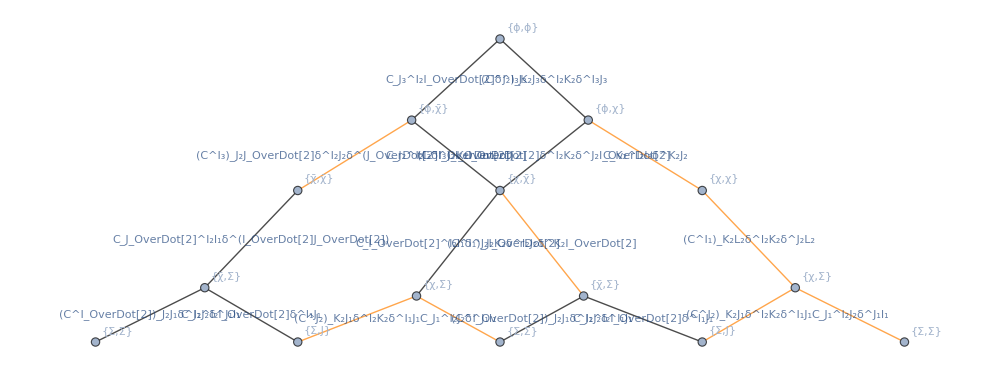

```mathematica
EdgeTaggedGraph[Join@@(signs/@pairs),VertexLabels->Automatic,VertexCoordinates->Thread[Tuples[Multiplet[2][[;;,1]],2]->({2(Last[#[[1]]]+Last[#[[2]]]),-3(ScalingDimension[#[[1]]]+ScalingDimension[#[[2]]])}&/@Tuples[Multiplet[2],2])],ImageSize->1000]
```

#### Automated Ward identities and solutions

```mathematica
AddSolutions[SolveWard[{"ϕ","χ"},"Defect"->True]]
AddSolutions[SolveWard[{"ϕ","χ̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ̄","Σ"},"Defect"->True]]
AddSolutions[SolveWard[{"χ","Σ"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ̄"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","Σ̄"},"Defect"->True]]
```

```mathematica
AddSolutions[SolveWard[{"χ","J"},"Defect"->True]]
AddSolutions[SolveWard[{"χ̄","J"},"Defect"->True]]
```

```mathematica
tt=Exp[-2I φ]g[Multiplet[1][[{6,6}]],1,1][u,v]+2g[Multiplet[1][[{5,6}]],1,1][u,v]+Exp[2I φ]g[Multiplet[1][[{5,5}]],1,1][u,v]/.{{0},_}->{0}
```

2 g_(1,1)^(Σ_1(Σ̄)_1)(u,v)+ⅇ^(-2 ⅈ φ) g_(1,1)^((Σ̄)_1(Σ̄)_1)(u,v)+ⅇ^(2 ⅈ φ) g_(1,1)^Σ_1Σ_1(u,v)

```mathematica
hSolved=Collect[tt/.(First/@SolvedCorrelators[])/.g[Multiplet[1][[{1,1}]]/.{{2},_}->{2},1,1]->a,Derivative[__][a][__],FullSimplify]
%/.{u->U,v->V}//InputForm
```

1/4 a^(1,0)(u,v) (4 u^2-4 u (u+v) cos(2 φ)+6 u v+3 v^2-1)+1/4 a^(0,1)(u,v) ((2 u v-v^2+1) cos(2 φ)-2 u v-3 v^2+1)-1/4 (v^2-1) a^(0,2)(u,v) (u (-cos(2 φ))+u+v)+1/4 (v^2-1) a^(1,1)(u,v) (u (-cos(2 φ))+u+v)-1/4 u (u+v) a^(2,0)(u,v) (u cos(2 φ)-u-v)+1/2 a(u,v) (u-(u+v) cos(2 φ))

(a[U, V]*(U - (U + V)*Cos[2*φ]))/2 + ((1 - 2*U*V - 3*V^2 + (1 + 2*U*V - V^2)*Cos[2*φ])*Derivative[0, 1][a][U, V])/4 - 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[0, 2][a][U, V])/4 + 
 ((-1 + 4*U^2 + 6*U*V + 3*V^2 - 4*U*(U + V)*Cos[2*φ])*Derivative[1, 0][a][U, V])/4 + 
 ((-1 + V^2)*(U + V - U*Cos[2*φ])*Derivative[1, 1][a][U, V])/4 - 
 (U*(U + V)*(-U - V + U*Cos[2*φ])*Derivative[2, 0][a][U, V])/4

```mathematica
Table[{k->SolvedCorrelators[][k][[1]][u,v]/.g[Multiplet[1][[{1,1}]]/.{{2},_}->{2},1,1]->({u,v}|->1/(16 u^2))},{k,Keys[SolvedCorrelators[]]}]//Simplify
```

{{g_(1,1)^(χ_2(χ̄)_2)→ⅈ/(64 u^3)},{g_(1,2)^(χ_2(χ̄)_2)→0},{g_(1,3)^(χ_2(χ̄)_2)→0},{g_(1,4)^(χ_2(χ̄)_2)→0},{g_(1,1)^χ_2χ_2→0},{g_(1,2)^χ_2χ_2→0},{g_(1,3)^χ_2χ_2→0},{g_(1,4)^χ_2χ_2→0},{g_(1,1)^((χ̄)_2(χ̄)_2)→0},{g_(1,2)^((χ̄)_2(χ̄)_2)→0},{g_(1,3)^((χ̄)_2(χ̄)_2)→0},{g_(1,4)^((χ̄)_2(χ̄)_2)→0},{g_(1,1)^Σ_1J_1→0},{g_(1,2)^Σ_1J_1→0},{g_(1,3)^Σ_1J_1→0},{g_(1,4)^Σ_1J_1→0},{g_(1,1)^(Σ_1(Σ̄)_1)→1/(64 u^3)},{g_(1,1)^Σ_1Σ_1→0},{g_(1,1)^((Σ̄)_1J_1)→0},{g_(1,2)^((Σ̄)_1J_1)→0},{g_(1,3)^((Σ̄)_1J_1)→0},{g_(1,4)^((Σ̄)_1J_1)→0},{g_(1,1)^((Σ̄)_1(Σ̄)_1)→0},{g_(1,1)^J_1J_1→0},{g_(1,2)^J_1J_1→0},{g_(1,3)^J_1J_1→0},{g_(1,4)^J_1J_1→0},{g_(1,5)^J_1J_1→0},{g_(1,6)^J_1J_1→0},{g_(1,7)^J_1J_1→0},{g_(1,8)^J_1J_1→0},{g_(1,9)^J_1J_1→0},{g_(1,10)^J_1J_1→0},{g_(1,11)^J_1J_1→0},{g_(1,12)^J_1J_1→0},{g_(1,13)^J_1J_1→1/(256 u^4)},{g_(1,14)^J_1J_1→0},{g_(1,15)^J_1J_1→0},{g_(1,16)^J_1J_1→0}}

```mathematica
Normal[SolvedCorrelators[]][[-23]]
Collect[8 u^2%[[2,1]][u,v]/.g[__]->Function[{u,v},a[u,v]/(u(u+v))],a[u,v]|Derivative[__][a][__],FullSimplify]
```

g_(1,1)^(ΣΣ̄)→{{u,v}↦1/8 (u^3 (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 u^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u^2 v (g_(1,1)^ϕϕ)^(2,0)(u,v)-v^3 (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^3 (g_(1,1)^ϕϕ)^(1,1)(u,v)-u v^2 (g_(1,1)^ϕϕ)^(0,2)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)+(-2 u v-3 v^2+1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+3 v^2 (g_(1,1)^ϕϕ)^(1,0)(u,v)+2 u g_(1,1)^ϕϕ(u,v)+u (g_(1,1)^ϕϕ)^(0,2)(u,v)+6 u v (g_(1,1)^ϕϕ)^(1,0)(u,v)-u (g_(1,1)^ϕϕ)^(1,1)(u,v)+v (g_(1,1)^ϕϕ)^(0,2)(u,v)-(g_(1,1)^ϕϕ)^(1,0)(u,v)-v (g_(1,1)^ϕϕ)^(1,1)(u,v))}

u^2 (u+v) a^(2,0)(u,v)+u (v^2-1) a^(1,1)(u,v)+(u-u v^2) a^(0,2)(u,v)+(1-v (2 u+v)) a^(0,1)(u,v)

```mathematica
Normal[SolvedCorrelators[]][[-22]]
Collect[8 u^2%[[2,1]][u,v]/.g[__]->Function[{u,v},a[u,v]/u^2],a[u,v]|Derivative[__][a][__],Simplify]
```

g_(1,1)^ΣΣ→{{u,v}↦1/8 (u (u^2 (g_(1,1)^ϕϕ)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕϕ)^(0,2)(u,v)+v^2 (g_(1,1)^ϕϕ)^(1,1)(u,v)+u v (g_(1,1)^ϕϕ)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕϕ)^(1,0)(u,v)-(g_(1,1)^ϕϕ)^(1,1)(u,v))+(-2 u v+v^2-1) (g_(1,1)^ϕϕ)^(0,1)(u,v)+2 (u+v) g_(1,1)^ϕϕ(u,v))}

u^2 (u+v) a^(2,0)(u,v)+u (v^2-1) a^(1,1)(u,v)+(-2 u v-v^2+1) a^(0,1)(u,v)+(u-u v^2) a^(0,2)(u,v)

```mathematica
SolvedCorrelators[]//Normal//TableForm
```

g_(1,1)^(χ_2(χ̄)_2)→{{u,v}↦1/8 ⅈ ((g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,2)^(χ_2(χ̄)_2)→{{u,v}↦1/8 ⅈ v (2 g_(1,1)^ϕ_3ϕ_3(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,3)^(χ_2(χ̄)_2)→{{u,v}↦0}
g_(1,4)^(χ_2(χ̄)_2)→{{u,v}↦0}
g_(1,1)^χ_2χ_2→{{u,v}↦0}
g_(1,2)^χ_2χ_2→{{u,v}↦0}
g_(1,3)^χ_2χ_2→{{u,v}↦-1/8 ⅈ (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)}
g_(1,4)^χ_2χ_2→{{u,v}↦-1/8 ⅈ v (2 g_(1,1)^ϕ_3ϕ_3(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,1)^((χ̄)_2(χ̄)_2)→{{u,v}↦0}
g_(1,2)^((χ̄)_2(χ̄)_2)→{{u,v}↦0}
g_(1,3)^((χ̄)_2(χ̄)_2)→{{u,v}↦-1/8 ⅈ (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)}
g_(1,4)^((χ̄)_2(χ̄)_2)→{{u,v}↦-1/8 ⅈ v (2 g_(1,1)^ϕ_3ϕ_3(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v))}
g_(1,1)^Σ_1J_1→{{u,v}↦0}
g_(1,2)^Σ_1J_1→{{u,v}↦0}
g_(1,3)^Σ_1J_1→{{u,v}↦-(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+4 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-2 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(16 √6)}
g_(1,4)^Σ_1J_1→{{u,v}↦(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+2 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-4 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(8 √6)}
g_(1,1)^(Σ_1(Σ̄)_1)→{{u,v}↦1/8 (u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+(-2 u v-3 v^2+1) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 u g_(1,1)^ϕ_3ϕ_3(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+6 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))}
g_(1,1)^Σ_1Σ_1→{{u,v}↦1/8 (-u (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+(2 u v-v^2+1) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-2 (u+v) g_(1,1)^ϕ_3ϕ_3(u,v))}
g_(1,1)^((Σ̄)_1J_1)→{{u,v}↦0}
g_(1,2)^((Σ̄)_1J_1)→{{u,v}↦0}
g_(1,3)^((Σ̄)_1J_1)→{{u,v}↦(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+4 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-2 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(16 √6)}
g_(1,4)^((Σ̄)_1J_1)→{{u,v}↦(u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+v^2 ((g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v))+2 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+v (-4 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(8 √6)}
g_(1,1)^((Σ̄)_1(Σ̄)_1)→{{u,v}↦1/8 (-u (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+(2 u v-v^2+1) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-2 (u+v) g_(1,1)^ϕ_3ϕ_3(u,v))}
g_(1,1)^J_1J_1→{{u,v}↦(v^2 (-2 v (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 u (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 g_(1,1)^ϕ_3ϕ_3(u,v)+(g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+2 v^3 ((g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+v^2 (4 (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-6 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v))+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(384 u)}
g_(1,2)^J_1J_1→{{u,v}↦-(v^2 (4 u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+16 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+6 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+4 u (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+20 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (2 u+v) g_(1,1)^ϕ_3ϕ_3(u,v)-4 v (2 u+v) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)))/(384 u)}
g_(1,3)^J_1J_1→{{u,v}↦0}
g_(1,4)^J_1J_1→{{u,v}↦0}
g_(1,5)^J_1J_1→{{u,v}↦(v^2 (-2 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+(8 v^2-6) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+4 v g_(1,1)^ϕ_3ϕ_3(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-4 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)))/(384 u)}
g_(1,6)^J_1J_1→{{u,v}↦0}
g_(1,7)^J_1J_1→{{u,v}↦0}
g_(1,8)^J_1J_1→{{u,v}↦(v^2 (-4 u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-8 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-6 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-4 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+2 (8 u v+4 v^2-3) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)-6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-16 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+u (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (2 u+v) g_(1,1)^ϕ_3ϕ_3(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)))/(384 u)}
g_(1,9)^J_1J_1→{{u,v}↦0}
g_(1,10)^J_1J_1→{{u,v}↦0}
g_(1,11)^J_1J_1→{{u,v}↦0}
g_(1,12)^J_1J_1→{{u,v}↦0}
g_(1,13)^J_1J_1→{{u,v}↦(2 u^3 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+8 u^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+4 u^2 v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+2 v^3 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)-2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+2 u v^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+(-4 u v-6 v^2+3) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+6 v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)+4 u g_(1,1)^ϕ_3ϕ_3(u,v)+2 u (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+12 u v (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 u (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+2 v (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)-3 (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-2 v (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))/(96 u)}
g_(1,14)^J_1J_1→{{u,v}↦0}
g_(1,15)^J_1J_1→{{u,v}↦0}
g_(1,16)^J_1J_1→{{u,v}↦(2 u (u^2 (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)-(v^2-1) (g_(1,1)^ϕ_3ϕ_3)^(0,2)(u,v)+v^2 (g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v)+u v (g_(1,1)^ϕ_3ϕ_3)^(2,0)(u,v)+4 (u+v) (g_(1,1)^ϕ_3ϕ_3)^(1,0)(u,v)-(g_(1,1)^ϕ_3ϕ_3)^(1,1)(u,v))+(-4 u v+2 v^2-3) (g_(1,1)^ϕ_3ϕ_3)^(0,1)(u,v)+4 (u+v) g_(1,1)^ϕ_3ϕ_3(u,v))/(96 u)}

## 𝒩 = 2

```mathematica
SetGlobalSymmetry[{SU2,U1}]
SetSignature["Euclidean"];
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{{2},0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"Σ\", TraditionalForm]\)",{{0},2},3,{0,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Σ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,0},-2]},"Flavor",True,1];
SetMultiplet[{{Operator["\!\(\*FormBox[OverscriptBox[\"𝒜\", \"_\"], TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[OverscriptBox[\"N\", \"_\"], TraditionalForm]\)",{{2},-2},3,{0,0},-2],Operator["\!\(\*FormBox[OverscriptBox[\"ξ\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{{1},-3},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[OverscriptBox[\"Y\", \"_\"], TraditionalForm]\)",{{0},-4},4,{0,0},-4]},{Operator["\!\(\*FormBox[\"𝒜\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[\"N\", TraditionalForm]\)",{{2},2},3,{0,0},2],Operator["\!\(\*FormBox[\"ξ\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{{1},3},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"Y\", TraditionalForm]\)",{{0},4},4,{0,0},4]}},"Chiral",False,2];
SetMultiplet[{Operator["\!\(\*FormBox[\"M\", TraditionalForm]\)",{{0},0},2,{0,0},0],Operator["\!\(\*FormBox[\"ζ\", TraditionalForm]\)",{{1},1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"ζ\", \"_\"], TraditionalForm]\)",{{1},-1},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"Z\", TraditionalForm]\)",{{0},2},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"Z\", \"_\"], TraditionalForm]\)",{{0},-2},3,{0,1},-2],Operator["\!\(\*FormBox[\"j1\", TraditionalForm]\)",{{0},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"j2\", TraditionalForm]\)",{{2},0},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"κ\", TraditionalForm]\)",{{1},1},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"κ\", \"_\"], TraditionalForm]\)",{{1},-1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{{0},0},4,{1,1},0]},"Stress Tensor",True,3];
```

```mathematica
DisplaySUSYVariations[]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

123

### Determine ⟨ϕϕϕϕ⟩

```mathematica
eqs=WardEquations[{"ϕ","ϕ","ϕ","χ̄"}]
```

{2 √2 v^3 g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-2 √2 g_(1,2)^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)+(√2 u g_(1,1)^(ϕϕχχ̄)(v/u,1/u))/v^2-√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_(3,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-(√2 g_(1,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_(3,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_(1,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)-((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_(3,1)^ϕϕϕϕ(u,v))/(√2)==0,-2 √2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) v^3-(2 √2 g_(2,2)^(ϕϕχχ̄)(u,v) v^3)/u^3==0,(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/u-√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)+√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)+(√2 g_(2,2)^(ϕϕχχ̄)(u,v))/u^2+(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,-√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/v+(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ √(3/2) g_(1,1)^ϕϕϕJ(u,v))/(v u)==0,-(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)+(g_(2,1)^(ϕϕχχ̄)(u,v))/(√2)-((u-1) g_(2,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0,(2 √2 g_(1,2)^(ϕϕχχ̄)(u,v) v^3)/u^3+2 √2 g_(2,2)^(ϕϕχχ̄)(1/u,v/u) v^3==0,-(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/u-(√2 g_(1,2)^(ϕϕχχ̄)(u,v))/u^2+√2 u g_(2,1)^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_(2,2)^(ϕϕχχ̄)(1/u,v/u)+(ⅈ (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_(2,2)^(ϕϕχχ̄)(1/u,v/u) u^2+(ⅈ √(3/2) g_(1,2)^ϕϕϕJ(u,v))/v+(ⅈ (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)+(ⅈ √(3/2) g_(1,1)^ϕϕϕJ(u,v))/(v u)==0,(g_(2,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_(2,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(ⅈ g_(1,1)^ϕϕϕϕ(u,v))/(√2)-(g_(1,1)^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_(1,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0,2 √2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) v^3+(2 √2 g_(1,2)^(ϕϕχχ̄)(u,v) v^3)/u^3-2 √2 g_(2,2)^(ϕϕχχ̄)(v/u,1/u)==0,√2 u g_(1,1)^(ϕϕχχ̄)(1/u,v/u)-√2 u (v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u)-(√2 g_(1,2)^(ϕϕχχ̄)(u,v))/u^2+(√2 u g_(2,1)^(ϕϕχχ̄)(v/u,1/u))/v^2+(ⅈ (g_(1,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(1,0)(u,v))/(√2)==0,√2 g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2-(√2 g_(2,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/v^3+(ⅈ (g_(1,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)-(ⅈ (g_(2,1)^ϕϕϕϕ)^(0,1)(u,v))/(√2)==0,(g_(1,1)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)-((-u+v+1) g_(1,2)^(ϕϕχχ̄)(1/u,v/u) u^2)/(√2)+(g_(2,1)^(ϕϕχχ̄)(v/u,1/u) u^2)/(√2 v^2)+(ⅈ g_(1,1)^ϕϕϕϕ(u,v))/(√2)-(ⅈ g_(2,1)^ϕϕϕϕ(u,v))/(√2)-(g_(1,1)^(ϕϕχχ̄)(u,v))/(√2)+((u-1) g_(1,2)^(ϕϕχχ̄)(u,v))/(√2 u)==0}

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,3}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v]}]
```

{g_(1,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^ϕϕϕϕ→({u,v}↦𝒯(u,v) f(3)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_(1,2)^(ϕϕχχ̄)(1/u,v/u),g_(1,2)^(ϕϕχχ̄)(v/u,1/u),g_(1,1)^(ϕϕχχ̄)(1/u,v/u),g_(1,1)^(ϕϕχχ̄)(v/u,1/u),g_(2,2)^(ϕϕχχ̄)(u,v),g_(1,2)^ϕϕϕJ(u,v),g_(1,1)^ϕϕϕJ(u,v),g_(2,1)^(ϕϕχχ̄)(u,v),g_(1,2)^(ϕϕχχ̄)(u,v),g_(2,2)^(ϕϕχχ̄)(1/u,v/u),g_(2,1)^(ϕϕχχ̄)(1/u,v/u),g_(1,1)^(ϕϕχχ̄)(u,v),g_(2,2)^(ϕϕχχ̄)(v/u,1/u),g_(2,1)^(ϕϕχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify)
```

{1/(2 √2 u)ⅈ (u (u 𝒯^(0,1)(u,v) f(1)(u,v)+((u-v) 𝒯^(0,1)(u,v)+(u-v+1) 𝒯^(1,0)(u,v)) f(2)(u,v)-(v 𝒯^(0,1)(u,v)+(u+v-1) 𝒯^(1,0)(u,v)) f(3)(u,v))+𝒯(u,v) (-2 (u-v+1) f(2)(u,v)+2 (v-1) f(3)(u,v)+u (u (f(1))^(0,1)(u,v)+(u-v) (f(2))^(0,1)(u,v)-v (f(3))^(0,1)(u,v)+u (f(2))^(1,0)(u,v)-v (f(2))^(1,0)(u,v)+(f(2))^(1,0)(u,v)-u (f(3))^(1,0)(u,v)-v (f(3))^(1,0)(u,v)+(f(3))^(1,0)(u,v)))),1/(√2 u v)ⅈ (u ((𝒯^(0,1)(u,v)+𝒯^(1,0)(u,v)) (-f(2)(u,v))+(v 𝒯^(0,1)(u,v)+(u-1) 𝒯^(1,0)(u,v)) f(3)(u,v)+((v-1) 𝒯^(0,1)(u,v)+u 𝒯^(1,0)(u,v)) f(1)(u,v))+𝒯(u,v) (2 f(2)(u,v)+2 f(3)(u,v)+u ((v-1) (f(1))^(0,1)(u,v)-(f(2))^(0,1)(u,v)+v (f(3))^(0,1)(u,v)+u (f(1))^(1,0)(u,v)-(f(2))^(1,0)(u,v)+u (f(3))^(1,0)(u,v)-(f(3))^(1,0)(u,v))))}

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform
```

{ⅈ (-2 (u-v+1) (α(2)+β(2) u+γ(2) v)+2 (v-1) (α(3)+β(3) u+γ(3) v)+u (β(2)+β(3)+β(2) u-β(3) u+γ(1) u+γ(2) (u-v)-β(2) v-β(3) v-γ(3) v))==0,ⅈ (2 (α(2)+β(2) u+γ(2) v)+2 (α(3)+β(3) u+γ(3) v)+u (-β(2)-β(3)-γ(2)+β(1) u+β(3) u+γ(1) (v-1)+γ(3) v))==0,ⅈ (u^2 (α(2)+β(2) u+γ(2) v)-u^2 (α(3)+β(3) u+γ(3) v)-u v (α(2)+β(2) u+γ(2) v)+u (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v)+u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(3)+β(3) u+γ(3) v)-u (α(2)+β(2) u+γ(2) v)-u (α(3)+β(3) u+γ(3) v))==0,ⅈ (u^2 (α(1)+β(1) u+γ(1) v)+u^2 (α(2)+β(2) u+γ(2) v)-u v (α(2)+β(2) u+γ(2) v)-u v (α(3)+β(3) u+γ(3) v))==0,ⅈ (-u (α(1)+β(1) u+γ(1) v)+u v (α(1)+β(1) u+γ(1) v)-u (α(2)+β(2) u+γ(2) v)+u v (α(3)+β(3) u+γ(3) v))==0}

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(2)→-α(1),α(3)→α(1),β(1)→-α(1),β(2)→α(1),β(3)→α(1),γ(1)→α(1),γ(2)→α(1),γ(3)→-α(1)}

```mathematica
Table[f[i][u,v],{i,3}]/.fform/.coeffSol/.α[1]->1
```

{-u+v+1,u+v-1,u-v+1}

### Find ,

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],(v/u)^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],u^-1 𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],u^-1 v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],u^-2 v 𝒯[u,v]];
```

```mathematica
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,3}]->{(1-u+v) 𝒯[u,v],(u+v-1)𝒯[u,v],(u-v+1)𝒯[u,v]}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","ϕ","χ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","χ","Σ̄"}]];
```

```mathematica
u[{1,3,2,4}]
v[{1,3,2,4}]
```

1/U

V/U

```mathematica
AddSolutions[SolveWard[{"ϕ","ϕ","J","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"ϕ","χ","χ","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ","χ̄","Σ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","Σ"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","Σ","Σ̄","Σ̄"}]];
```

```mathematica
SetDirectory["C:/users/rossd/documents/ward"]
```

C:\users\rossd\documents\ward

```mathematica
<<scwige_state_n2flavor.mx
```

```mathematica
Contract[TensorProduct[ExpandCorrelator@Correlator@Tensor[{"ϕ","ϕ","ϕ","J"}],σ[Bar]],{{5,9},{6,8}}]
```

g_(1,1)^ϕϕϕJ(U,V) C_1^(i_(3⊗0)j_(3⊗0)k_(3⊗0)i_(1⊗0))(𝒮_({1,2,3,4};1)^({2,{0,0}};{2,{0,0}};{2,{0,0}};{3,{1/2,1/2}}))_(αα̇)((σ̄)_μ)^(α̇α)+g_(1,2)^ϕϕϕJ(U,V) C_1^(i_(3⊗0)j_(3⊗0)k_(3⊗0)i_(1⊗0))(𝒮_({1,2,3,4};2)^({2,{0,0}};{2,{0,0}};{2,{0,0}};{3,{1/2,1/2}}))_(αα̇)((σ̄)_μ)^(α̇α)

```mathematica
ϕϕϕJ=Normal[CanonicallyOrderedComponents[Contract[TensorProduct[ExpandCorrelator@Correlator@Tensor[{"ϕ","ϕ","ϕ","J"}],σ[Bar]],{{5,9},{6,8}}]][[;;,1,1,2,3]]]/.Normal[First/@SolvedCorrelators[]];
```

```mathematica
Export["ϕϕϕJ.m",ϕϕϕJ]
```

ϕϕϕJ.m

```mathematica
ϕϕJϕ=Normal[CanonicallyOrderedComponents[CrossingSimplify[Contract[TensorProduct[ExpandCorrelator@Correlator@Tensor[{"ϕ","ϕ","J","ϕ"}],σ[Bar]],{{5,9},{6,8}}]/.Normal[First/@SolvedCorrelators[]]/.{u[{1,2,4,3}]->u/v,v[{1,2,4,3}]->1/v}]/.{u->u[{1,2,3,4}],v->v[{1,2,3,4}]}][[;;,1,1,2,3]]];
```

```mathematica
Export["ϕϕJϕ.m",ϕϕJϕ]
```

ϕϕJϕ.m

```mathematica
Contract[TensorProduct[ExpandCorrelator@Correlator@Tensor[{"ϕ","ϕ","J","J"}],σ[Bar],σ[Bar]],{{5,11},{6,10},{7,14},{8,13}}]
```

C_1^(i_(3⊗0)j_(3⊗0)i_(1⊗0)j_(1⊗0))(𝒮_({1,2,3,4};1)^({2,{0,0}};{2,{0,0}};{3,{1/2,1/2}};{3,{1/2,1/2}}))_(αα̇ββ̇)((σ̄)_μ)^(α̇α)((σ̄)_ν)^(β̇β) g_(1,1)^ϕϕJJ(U,V)+C_1^(i_(3⊗0)j_(3⊗0)i_(1⊗0)j_(1⊗0))(𝒮_({1,2,3,4};2)^({2,{0,0}};{2,{0,0}};{3,{1/2,1/2}};{3,{1/2,1/2}}))_(αα̇ββ̇)((σ̄)_μ)^(α̇α)((σ̄)_ν)^(β̇β) g_(1,2)^ϕϕJJ(U,V)+C_1^(i_(3⊗0)j_(3⊗0)i_(1⊗0)j_(1⊗0))(𝒮_({1,2,3,4};3)^({2,{0,0}};{2,{0,0}};{3,{1/2,1/2}};{3,{1/2,1/2}}))_(αα̇ββ̇)((σ̄)_μ)^(α̇α)((σ̄)_ν)^(β̇β) g_(1,3)^ϕϕJJ(U,V)+C_1^(i_(3⊗0)j_(3⊗0)i_(1⊗0)j_(1⊗0))(𝒮_({1,2,3,4};4)^({2,{0,0}};{2,{0,0}};{3,{1/2,1/2}};{3,{1/2,1/2}}))_(αα̇ββ̇)((σ̄)_μ)^(α̇α)((σ̄)_ν)^(β̇β) g_(1,4)^ϕϕJJ(U,V)+C_1^(i_(3⊗0)j_(3⊗0)i_(1⊗0)j_(1⊗0))(𝒮_({1,2,3,4};5)^({2,{0,0}};{2,{0,0}};{3,{1/2,1/2}};{3,{1/2,1/2}}))_(αα̇ββ̇)((σ̄)_μ)^(α̇α)((σ̄)_ν)^(β̇β) g_(1,5)^ϕϕJJ(U,V)+C_1^(i_(3⊗0)j_(3⊗0)i_(1⊗0)j_(1⊗0))(𝒮_({1,2,3,4};6)^({2,{0,0}};{2,{0,0}};{3,{1/2,1/2}};{3,{1/2,1/2}}))_(αα̇ββ̇)((σ̄)_μ)^(α̇α)((σ̄)_ν)^(β̇β) g_(1,6)^ϕϕJJ(U,V)

```mathematica
ϕϕJJ=Normal[CanonicallyOrderedComponents[Contract[TensorProduct[ExpandCorrelator@Correlator@Tensor[{"ϕ","ϕ","J","J"}],σ[Bar],σ[Bar]],{{5,11},{6,10},{7,14},{8,13}}]][[;;,;;,1,1,1,3]]]/.Normal[First/@SolvedCorrelators[]];
```

```mathematica
Export["ϕϕJJ.m",ϕϕJJ]
```

ϕϕJJ.m

### Find

```mathematica
DeclareArbitraryFunction[𝒫];
DeclareCrossingRule[𝒫[v,u],𝒫[v,u]];
DeclareCrossingRule[𝒫[u/v,1/v],𝒫[u,v]];
DeclareCrossingRule[𝒫[1/u,v/u],𝒫[1/u,v/u]];
DeclareCrossingRule[𝒫[v/u,1/u],𝒫[v,u]];
DeclareCrossingRule[𝒫[1/v,u/v],𝒫[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[1][[1]],Multiplet[1][[1]]},1,1][u,v]->𝒫[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ϕ","χ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ","Σ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","χ̄","Σ"},"QBar"->True]]
```

### Stress tensor

```mathematica
DeclareArbitraryFunction[𝒬];
DeclareCrossingRule[𝒬[v,u],v^2/u^2 𝒬[u,v]];
DeclareCrossingRule[𝒬[u/v,1/v],𝒬[u,v]];
DeclareCrossingRule[𝒬[1/u,v/u],1/u^2 𝒬[u,v]];
DeclareCrossingRule[𝒬[v/u,1/u],v^2/u^2 𝒬[u,v]];
DeclareCrossingRule[𝒬[1/v,u/v],1/u^2 𝒬[u,v]];
```

```mathematica
DeclareArbitraryFunction[ℛ];
DeclareCrossingRule[ℛ[v,u],ℛ[v,u]];
DeclareCrossingRule[ℛ[u/v,1/v],-ℛ[u,v]];
DeclareCrossingRule[ℛ[1/u,v/u],(-(u^3 ℛ[v,u]-v^3 ℛ[u,v]))/(u^3 v^3)];
DeclareCrossingRule[ℛ[v/u,1/u],-ℛ[v,u]];
DeclareCrossingRule[ℛ[1/v,u/v],(u^3 ℛ[v,u]-v^3 ℛ[u,v])/(u^3 v^3)];
```

```mathematica
SCWIGEE`Private`$SolvedCorrelators=<||>
```

<||>

```mathematica
AddSolutions[{g[Multiplet[3][[{1,1,1,1}]],1,1][u,v]->𝒬[u,v]}];
```

```mathematica
AddSolutions[{g[Multiplet[3][[{1,1,2,3}]],1,2][u,v]->ℛ[u,v]}];
```

```mathematica
corr=ExpandCorrelator@Correlator@Tensor[Multiplet[3][[{1,1,2,3}]]];
crossEqs=Flatten@Table[Thread[Flatten@Normal@ExpansionComponents[(corr/.{1,2,3,4}->p)-(corr/.{1,2,3,4}->(p[[{2,1,3,4}]]))]==0],{p,Permutations@Range[4]}];
```

```mathematica
eqs=CrossingSimplify[Flatten[{
crossEqs,
WardEquations[{"M","M","M","ζ̄"}],
WardEquations[{"M","M","M","ζ"},"QBar"->True]
}]/.Normal[First/@SolvedCorrelators[]]];
vars=DeleteDuplicates@Cases[eqs,g[__][__],All];
{bb,mm}=CoefficientArrays[eqs,vars];
MatrixRank[mm]
Length[vars]
```

8

8

```mathematica
vars
```

{g_(1,1)^(MMζζ̄)(u,v),g_(1,1)^(MMζζ̄)(u/v,1/v),g_(1,1)^(MMζζ̄)(1/u,v/u),g_(1,1)^(MMζζ̄)(1/v,u/v),g_(1,1)^(MMζζ̄)(v,u),g_(1,1)^(MMζζ̄)(v/u,1/u),g_(1,2)^MMMj1(u,v),g_(1,1)^MMMj1(u,v)}

```mathematica
sol=First@Solve[eqs,vars];
crossedSol=Simplify@CrossingSimplify[#/.First@Solve[Thread[List@@#[[1]]=={uu,vv}],{u,v}]/.{uu->u,vv->v}]&/@sol;
```

```mathematica
AddSolutions[sol]
```

```mathematica
eqs=CrossingSimplify[Flatten[{
WardEquations[{"M","M","ζ̄","j1"}],
WardEquations[{"M","M","ζ","j1"},"QBar"->True],
WardEquations[{"M","M","ζ̄","j2"}],
WardEquations[{"M","M","ζ","j2"},"QBar"->True],
WardEquations[{"M","M","ζ","Z̄"}],
WardEquations[{"M","M","ζ̄","Z"},"QBar"->True]
}]/.Normal[First/@SolvedCorrelators[]]];
vars=DeleteDuplicates@Cases[eqs,g[__][__],All];
{bb,mm}=CoefficientArrays[eqs,vars];
MatrixRank[mm]
Length[vars]
```

64

90

```mathematica
Sort/@GroupBy[vars,#[[0,1]]&]//Normal//TableForm
```

{M_^(1⊗0),M_^(1⊗0),j1_(αα̇)^(1⊗0),j1_(αα̇)^(1⊗0)}→{g_(1,1)^MMj1j1(u,v),g_(1,2)^MMj1j1(u,v),g_(1,3)^MMj1j1(u,v),g_(1,4)^MMj1j1(u,v),g_(1,5)^MMj1j1(u,v),g_(1,6)^MMj1j1(u,v)}
{M_^(1⊗0),ζ_α^(2⊗1),(ζ̄)_(α̇)^(2⊗-1),j1_(αα̇)^(1⊗0)}→{g_(1,1)^(Mζζ̄j1)(1/u,v/u),g_(1,1)^(Mζζ̄j1)(u,v),g_(1,1)^(Mζζ̄j1)(u/v,1/v),g_(1,1)^(Mζζ̄j1)(v/u,1/u),g_(1,2)^(Mζζ̄j1)(1/u,v/u),g_(1,2)^(Mζζ̄j1)(u,v),g_(1,2)^(Mζζ̄j1)(u/v,1/v),g_(1,2)^(Mζζ̄j1)(v/u,1/u),g_(1,3)^(Mζζ̄j1)(1/u,v/u),g_(1,3)^(Mζζ̄j1)(u,v),g_(1,3)^(Mζζ̄j1)(u/v,1/v),g_(1,3)^(Mζζ̄j1)(v/u,1/u),g_(1,4)^(Mζζ̄j1)(1/u,v/u),g_(1,4)^(Mζζ̄j1)(u,v),g_(1,4)^(Mζζ̄j1)(u/v,1/v),g_(1,4)^(Mζζ̄j1)(v/u,1/u),g_(1,5)^(Mζζ̄j1)(1/u,v/u),g_(1,5)^(Mζζ̄j1)(u,v),g_(1,5)^(Mζζ̄j1)(u/v,1/v),g_(1,5)^(Mζζ̄j1)(v/u,1/u),g_(1,6)^(Mζζ̄j1)(1/u,v/u),g_(1,6)^(Mζζ̄j1)(u,v),g_(1,6)^(Mζζ̄j1)(u/v,1/v),g_(1,6)^(Mζζ̄j1)(v/u,1/u)}
{M_^(1⊗0),M_^(1⊗0),(ζ̄)_(α̇)^(2⊗-1),κ_(αβα̇)^(2⊗1)}→{g_(1,1)^(MMζ̄κ)(u,v),g_(1,2)^(MMζ̄κ)(u,v),g_(1,3)^(MMζ̄κ)(u,v),g_(1,4)^(MMζ̄κ)(u,v)}
{M_^(1⊗0),M_^(1⊗0),ζ_α^(2⊗1),(κ̄)_(αα̇β̇)^(2⊗-1)}→{g_(1,1)^(MMζκ̄)(u,v),g_(1,2)^(MMζκ̄)(u,v),g_(1,3)^(MMζκ̄)(u,v),g_(1,4)^(MMζκ̄)(u,v)}
{M_^(1⊗0),M_^(1⊗0),j2_(αα̇)^(3⊗0),j2_(αα̇)^(3⊗0)}→{g_(1,1)^MMj2j2(u,v),g_(1,2)^MMj2j2(u,v),g_(1,3)^MMj2j2(u,v),g_(1,4)^MMj2j2(u,v),g_(1,5)^MMj2j2(u,v),g_(1,6)^MMj2j2(u,v)}
{M_^(1⊗0),ζ_α^(2⊗1),(ζ̄)_(α̇)^(2⊗-1),j2_(αα̇)^(3⊗0)}→{g_(1,1)^(Mζζ̄j2)(1/u,v/u),g_(1,1)^(Mζζ̄j2)(u,v),g_(1,1)^(Mζζ̄j2)(u/v,1/v),g_(1,1)^(Mζζ̄j2)(v/u,1/u),g_(1,2)^(Mζζ̄j2)(1/u,v/u),g_(1,2)^(Mζζ̄j2)(u,v),g_(1,2)^(Mζζ̄j2)(u/v,1/v),g_(1,2)^(Mζζ̄j2)(v/u,1/u),g_(1,3)^(Mζζ̄j2)(1/u,v/u),g_(1,3)^(Mζζ̄j2)(u,v),g_(1,3)^(Mζζ̄j2)(u/v,1/v),g_(1,3)^(Mζζ̄j2)(v/u,1/u),g_(1,4)^(Mζζ̄j2)(1/u,v/u),g_(1,4)^(Mζζ̄j2)(u,v),g_(1,4)^(Mζζ̄j2)(u/v,1/v),g_(1,4)^(Mζζ̄j2)(v/u,1/u),g_(1,5)^(Mζζ̄j2)(1/u,v/u),g_(1,5)^(Mζζ̄j2)(u,v),g_(1,5)^(Mζζ̄j2)(u/v,1/v),g_(1,5)^(Mζζ̄j2)(v/u,1/u),g_(1,6)^(Mζζ̄j2)(1/u,v/u),g_(1,6)^(Mζζ̄j2)(u,v),g_(1,6)^(Mζζ̄j2)(u/v,1/v),g_(1,6)^(Mζζ̄j2)(v/u,1/u)}
{M_^(1⊗0),M_^(1⊗0),Z_αβ^(1⊗2),(Z̄)_(α̇β̇)^(1⊗-2)}→{g_(1,1)^(MMZZ̄)(u,v),g_(1,1)^(MMZZ̄)(u/v,1/v),g_(1,2)^(MMZZ̄)(u,v),g_(1,2)^(MMZZ̄)(u/v,1/v),g_(1,3)^(MMZZ̄)(u,v),g_(1,3)^(MMZZ̄)(u/v,1/v)}
{M_^(1⊗0),ζ_α^(2⊗1),ζ_α^(2⊗1),(Z̄)_(α̇β̇)^(1⊗-2)}→{g_(1,1)^(MζζZ̄)(u,v),g_(1,1)^(MζζZ̄)(u/v,1/v),g_(1,2)^(MζζZ̄)(u,v),g_(1,2)^(MζζZ̄)(u/v,1/v),g_(1,3)^(MζζZ̄)(u,v),g_(1,3)^(MζζZ̄)(u/v,1/v),g_(1,4)^(MζζZ̄)(u,v),g_(1,4)^(MζζZ̄)(u/v,1/v)}
{M_^(1⊗0),(ζ̄)_(α̇)^(2⊗-1),(ζ̄)_(α̇)^(2⊗-1),Z_αβ^(1⊗2)}→{g_(1,1)^(Mζ̄ζ̄Z)(u,v),g_(1,1)^(Mζ̄ζ̄Z)(u/v,1/v),g_(1,2)^(Mζ̄ζ̄Z)(u,v),g_(1,2)^(Mζ̄ζ̄Z)(u/v,1/v),g_(1,3)^(Mζ̄ζ̄Z)(u,v),g_(1,3)^(Mζ̄ζ̄Z)(u/v,1/v),g_(1,4)^(Mζ̄ζ̄Z)(u,v),g_(1,4)^(Mζ̄ζ̄Z)(u/v,1/v)}

### Find , ,

```mathematica
DeclareArbitraryFunction[𝒲];
DeclareCrossingRule[𝒲[v,u],𝒲[v,u]];
DeclareCrossingRule[𝒲[u/v,1/v],𝒲[u,v]];
DeclareCrossingRule[𝒲[1/u,v/u],𝒲[1/u,v/u]];
DeclareCrossingRule[𝒲[v/u,1/u],𝒲[v,u]];
DeclareCrossingRule[𝒲[1/v,u/v],𝒲[1/u,v/u]];
```

```mathematica
AddSolutions[{g[{Multiplet[2][[2,1]],Multiplet[2][[1,1]],Multiplet[3][[1]],Multiplet[3][[1]]},1,1][u,v]->𝒲[u,v]}];
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ̄"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","M","ζ"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","Z̄"}]]
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","Z"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j1"}]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ","j1"},"QBar"->True]]
```

```mathematica
AddSolutions[SolveWard[{"𝒜","𝒜̄","ζ̄","j2"}]]
```

$Aborted

```mathematica
Put[SolvedCorrelators[],"n2_correlators_test.m"]
```

## 𝒩 = 4 Vector

```mathematica
SetGlobalSymmetry[SU4]
SetMultiplet[{Operator["\!\(\*FormBox[\"X\", TraditionalForm]\)",{0,1,0},1,{0,0},0],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},3/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},3/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,0,0},2,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,0,0},2,{0,1},-2]},"Vector",True,1];
```

```mathematica
DisplaySUSYVariations[]
```

1

## 𝒩 = 4 Stress tensor

```mathematica
SetSpacetimeDimension[4];
SetGlobalSymmetry[SU4];
SetSignature["Euclidean"];
SetMultiplet[{Operator["\!\(\*FormBox[\"S\", TraditionalForm]\)",{0,2,0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0,1,1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{1,1,0},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{1,0,1},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P\", TraditionalForm]\)",{0,0,2},3,{0,0},2],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,1,0},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,1,0},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"P\", \"_\"], TraditionalForm]\)",{2,0,0},3,{0,0},-2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{1,0,0},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{0,0,1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{0,0,0},4,{0,0},4],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{0,0,0},4,{1,1},0],Operator["\!\(\*FormBox[OverscriptBox[\"ϕ\", \"_\"], TraditionalForm]\)",{0,0,0},4,{0,0},-4]},"Stress Tensor",True,1];
```

```mathematica
Get["C:/users/rossd/downloads/ThreePtStructures2.txt"];
Get["C:/users/rossd/downloads/FourPtStructures2.txt"];
```

```mathematica
SetTwoPtGlobalInvariant[6,6,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6}]]];
SetTwoPtGlobalInvariant[4,-4,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4}]]];
SetTwoPtGlobalInvariant[1,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,1},{j,1,1}]]];
SetTwoPtGlobalInvariant[10,-10,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10}]]];
SetTwoPtGlobalInvariant[15,15,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15}]]];
SetTwoPtGlobalInvariant[20,-20,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
SetTwoPtGlobalInvariant[{0,2,0},{0,2,0},SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20}]]];
```

```mathematica
SetThreePtGlobalInvariant[4,{0,2,0},-20,SparseArray[threeptinvt420p20b]];
SetThreePtGlobalInvariant[4,20,10,SparseArray[threeptinvt42010]];
SetThreePtGlobalInvariant[4,20,6,SparseArray[threeptinvt4206]];
SetThreePtGlobalInvariant[4,6,4,SparseArray[threeptinvt464]];
SetThreePtGlobalInvariant[4,-4,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,4},{j,1,4},{k,1,1}]]];
SetThreePtGlobalInvariant[4,-20,15,SparseArray[Conjugate[threeptinvt4b2015]]];
SetThreePtGlobalInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtGlobalInvariant[4,-10,4,SparseArray[threeptinvt410b4]];
SetThreePtGlobalInvariant[-4,{0,2,0},20,SparseArray[Conjugate[threeptinvt420p20b]]];
SetThreePtGlobalInvariant[-4,-20,-10,SparseArray[Conjugate[threeptinvt42010]]];
SetThreePtGlobalInvariant[-4,-20,-6,SparseArray[Conjugate[threeptinvt4206]]];
SetThreePtGlobalInvariant[-4,6,-4,SparseArray[Conjugate[threeptinvt464]]];
SetThreePtGlobalInvariant[-4,20,15,SparseArray[threeptinvt4b2015]];
SetThreePtGlobalInvariant[4,15,-4,SparseArray[threeptinvt4154b]];
SetThreePtGlobalInvariant[-4,10,-4,SparseArray[Conjugate[threeptinvt410b4]]];
```

```mathematica
SetThreePtGlobalInvariant[{0,2,0},6,6,SparseArray[threeptinvt20p66]];
SetThreePtGlobalInvariant[15,6,6,SparseArray[threeptinvt1566]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},15,SparseArray[threeptinvt20p20p15]];
SetThreePtGlobalInvariant[{0,2,0},15,15,SparseArray[threeptinvt20p1515]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},{0,2,0},SparseArray[threeptinvt20p20p20p]];
SetThreePtGlobalInvariant[{0,2,0},{0,2,0},1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtGlobalInvariant[20,-20,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,20},{j,1,20},{k,1,1}]]];
SetThreePtGlobalInvariant[15,15,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,15},{j,1,15},{k,1,1}]]];
SetThreePtGlobalInvariant[6,6,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,6},{j,1,6},{k,1,1}]]];
SetThreePtGlobalInvariant[10,-10,1,SparseArray[Table[KroneckerDelta[i,j],{i,1,10},{j,1,10},{k,1,1}]]];
SetThreePtGlobalInvariant[{0,2,0},20,-20,SparseArray[threeptinvt20p2020b]];
SetThreePtGlobalInvariant[{0,2,0},10,10,SparseArray[threeptinvt20p1010]];
SetThreePtGlobalInvariant[{0,2,0},-10,-10,SparseArray[Conjugate[threeptinvt20p1010]]];
SetThreePtGlobalInvariant[20,20,6,SparseArray[threeptinvt20206]];
SetThreePtGlobalInvariant[-20,-20,6,SparseArray[Conjugate[threeptinvt20206]]];
SetThreePtGlobalInvariant[20,20,10,SparseArray[threeptinvt202010]];
SetThreePtGlobalInvariant[-20,-20,-10,SparseArray[Conjugate[threeptinvt202010]]];
SetThreePtGlobalInvariant[10,-10,15,SparseArray[threeptinvt1010b15]];
SetThreePtGlobalInvariant[6,10,15,SparseArray[threeptinvt61015]];
SetThreePtGlobalInvariant[6,-10,15,SparseArray[Conjugate[threeptinvt61015]]];
```

```mathematica
SetThreePtGlobalInvariant[20,20,-10,SparseArray[threeptinvt202010b]];
SetThreePtGlobalInvariant[-20,-20,10,SparseArray[Conjugate@threeptinvt202010b]];
```

```mathematica
DisplaySUSYVariations[]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1

### Find

```mathematica
eqs=WardEquations[{"S","S","S","χ̄"},"UseSUSYRules"->False];
```

```mathematica
trial=Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1],{i,6}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v],{u,v}|->f[4][u,v]𝒯[u,v],{u,v}|->f[5][u,v]𝒯[u,v],{u,v}|->f[6][u,v]𝒯[u,v]}]
```

{g_(1,1)^SSSS→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^SSSS→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^SSSS→({u,v}↦𝒯(u,v) f(3)(u,v)),g_(4,1)^SSSS→({u,v}↦𝒯(u,v) f(4)(u,v)),g_(5,1)^SSSS→({u,v}↦𝒯(u,v) f(5)(u,v)),g_(6,1)^SSSS→({u,v}↦𝒯(u,v) f(6)(u,v))}

```mathematica
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All]
```

{g_(1,2)^(SSχχ̄)(1/u,v/u),g_(1,2)^(SSχχ̄)(u,v),g_(2,2)^(SSχχ̄)(1/u,v/u),g_(2,2)^(SSχχ̄)(u,v),g_(1,1)^(SSχχ̄)(1/u,v/u),g_(2,1)^(SSχχ̄)(1/u,v/u),g_(1,1)^(SSχχ̄)(u,v),g_(2,1)^(SSχχ̄)(u,v),g_(1,2)^(SSχχ̄)(v/u,1/u),g_(2,2)^(SSχχ̄)(v/u,1/u),g_(3,2)^(SSχχ̄)(1/u,v/u),g_(3,2)^(SSχχ̄)(u,v),g_(1,1)^(SSχχ̄)(v/u,1/u),g_(2,1)^(SSχχ̄)(v/u,1/u),g_(3,1)^(SSχχ̄)(1/u,v/u),g_(3,1)^(SSχχ̄)(u,v),g_(3,2)^(SSχχ̄)(v/u,1/u),g_(3,1)^(SSχχ̄)(v/u,1/u),g_(4,2)^(SSχχ̄)(u,v),g_(1,2)^SSSJ(u,v),g_(1,1)^SSSJ(u,v),g_(4,1)^(SSχχ̄)(u,v),g_(4,2)^(SSχχ̄)(1/u,v/u),g_(3,2)^SSSJ(u,v),g_(4,1)^(SSχχ̄)(1/u,v/u),g_(3,1)^SSSJ(u,v),g_(4,2)^(SSχχ̄)(v/u,1/u),g_(4,1)^(SSχχ̄)(v/u,1/u),g_(5,2)^(SSχχ̄)(u,v),g_(2,2)^SSSJ(u,v),g_(2,1)^SSSJ(u,v),g_(5,1)^(SSχχ̄)(u,v),g_(5,2)^(SSχχ̄)(1/u,v/u),g_(5,1)^(SSχχ̄)(1/u,v/u),g_(5,2)^(SSχχ̄)(v/u,1/u),g_(5,1)^(SSχχ̄)(v/u,1/u),g_(6,2)^(SSχχ̄)(u,v),g_(6,1)^(SSχχ̄)(u,v),g_(6,2)^(SSχχ̄)(1/u,v/u),g_(6,1)^(SSχχ̄)(1/u,v/u),g_(6,2)^(SSχχ̄)(v/u,1/u),g_(6,1)^(SSχχ̄)(v/u,1/u)}

```mathematica
{bb,mm}=CoefficientArrays[eqs/.trial,vars]
```

{SparseArray[…],SparseArray[…]}

```mathematica
sbz=(NullSpace[Transpose[mm]].bb//Simplify);
```

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v+δ[i] u v+ζ[i] u^2+ξ[i] v^2));
coeffEqs=DeleteCases[Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform,True];
```

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]/.γ[1]->1,Flatten@Table[{α[i],β[i],γ[i],δ[i],ζ[i],ξ[i]},{i,6}]]
```

{α(1)→0,β(1)→0,δ(1)→0,ζ(1)→0,ξ(1)→0,α(2)→0,β(2)→0,γ(2)→0,δ(2)→1,ζ(2)→0,ξ(2)→0,α(3)→0,β(3)→1,γ(3)→0,δ(3)→0,ζ(3)→0,ξ(3)→0,α(4)→1/16,β(4)→-1/16,γ(4)→-1/16,δ(4)→0,ζ(4)→0,ξ(4)→0,α(5)→0,β(5)→0,γ(5)→-1/16,δ(5)→-1/16,ζ(5)→0,ξ(5)→1/16,α(6)→0,β(6)→-1/16,γ(6)→0,δ(6)→-1/16,ζ(6)→1/16,ξ(6)→0}

```mathematica
multipliers=Table[f[i][u,v],{i,6}]/.fform/.coeffSol/.γ[1]->1//Simplify
```

{v,u v,u,1/16 (-u-v+1),1/16 v (-u+v-1),1/16 u (u-v-1)}

### Solve identities

```mathematica
DeclareArbitraryFunction[𝒯];
AddSolutions[Thread[Table[g[Multiplet[1][[{1,1,1,1}]],i,1][u,v],{i,6}]->(multipliers 𝒯[u,v])]];
```

```mathematica
DeclareCrossingRule@@@CrossingRelations[Multiplet[1][[{1,1,1,1}]]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","S","χ̄"}]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ"}]]
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P̄","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","P","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","P","P̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","F̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"S","S","χ̄","J"}]]
```

```mathematica
AddSolutions[SolveWard[{"S","χ","χ̄","χ̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P̄","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","P","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","χ","P̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"P","P","χ̄","P̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","F","χ̄"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","F̄","χ"}]];
```

```mathematica
AddSolutions[SolveWard[{"P","P̄","χ̄","J"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ","F̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","F"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","χ̄","χ̄","J"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ","P","F̄","F̄"}]];
```

```mathematica
AddSolutions[SolveWard[{"χ̄","P̄","F","F"},"QBar"->True]];
```

```mathematica
AddSolutions[SolveWard[{"χ","F","F̄","F̄"}]];
```

$Aborted

```mathematica
AddSolutions[SolveWard[{"χ̄","F","F","F̄"},"QBar"->True]]
```

```mathematica
DeleteFile["scwige_state2.mx"];
DumpSave["scwige_state2.mx",{"Global`","SCWIGE`"}];
```

```mathematica
repeats=Select[SolvedCorrelators[],Length[#]>1&];
Flatten@Table[FullSimplify[Differences@Table[ff[u,v],{ff,repeats[Keys[repeats][[i]]]}],u>0&&v>0],{i,Length[repeats]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## 𝒩 = 4 S_3

```mathematica
SetGlobalSymmetry[SU4]
SetSignature["Euclidean"];
SetMultiplet[{Operator["\!\(\*FormBox[\"S\", TraditionalForm]\)",{0,2,0},2,{0,0},0],Operator["\!\(\*FormBox[\"χ\", TraditionalForm]\)",{0,1,1},5/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ\", \"_\"], TraditionalForm]\)",{1,1,0},5/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J\", TraditionalForm]\)",{1,0,1},3,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P\", TraditionalForm]\)",{0,0,2},3,{0,0},2],Operator["\!\(\*FormBox[\"F\", TraditionalForm]\)",{0,1,0},3,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"F\", \"_\"], TraditionalForm]\)",{0,1,0},3,{0,1},-2],Operator["\!\(\*FormBox[OverscriptBox[\"P\", \"_\"], TraditionalForm]\)",{2,0,0},3,{0,0},-2],Operator["\!\(\*FormBox[\"λ\", TraditionalForm]\)",{0,0,1},7/2,{1/2,0},3],Operator["\!\(\*FormBox[\"ψ\", TraditionalForm]\)",{1,0,0},7/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ\", \"_\"], TraditionalForm]\)",{0,0,1},7/2,{1/2,1},-1],Operator["\!\(\*FormBox[OverscriptBox[\"λ\", \"_\"], TraditionalForm]\)",{1,0,0},7/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ϕ\", TraditionalForm]\)",{0,0,0},4,{0,0},4],Operator["\!\(\*FormBox[\"T\", TraditionalForm]\)",{0,0,0},4,{1,1},0],Operator["\!\(\*FormBox[OverscriptBox[\"ϕ\", \"_\"], TraditionalForm]\)",{0,0,0},4,{0,0},-4]},"Stress Tensor",True,1];
```

```mathematica
SetMultiplet[{Operator["\!\(\*FormBox[\"S3\", TraditionalForm]\)",{0,3,0},3,{0,0},0],Operator["\!\(\*FormBox[\"χ3\", TraditionalForm]\)",{0,2,1},7/2,{1/2,0},1],Operator["\!\(\*FormBox[OverscriptBox[\"χ3\", \"_\"], TraditionalForm]\)",{1,2,0},7/2,{0,1/2},-1],Operator["\!\(\*FormBox[\"J3\", TraditionalForm]\)",{1,1,1},4,{1/2,1/2},0],Operator["\!\(\*FormBox[\"P3\", TraditionalForm]\)",{0,1,2},4,{0,0},2],
Operator["\!\(\*FormBox[OverscriptBox[\"P3\", \"_\"], TraditionalForm]\)",{2,1,0},4,{0,0},-2],Operator["\!\(\*FormBox[\"B3\", TraditionalForm]\)",{0,2,0},4,{1,0},2],Operator["\!\(\*FormBox[OverscriptBox[\"B3\", \"_\"], TraditionalForm]\)",{0,2,0},4,{0,1},-2],Operator["\!\(\*FormBox[\"λ3\", TraditionalForm]\)",{0,1,1},9/2,{1/2,0},3],Operator["\!\(\*FormBox[OverscriptBox[\"λ3\", \"_\"], TraditionalForm]\)",{1,1,0},9/2,{0,1/2},-3],Operator["\!\(\*FormBox[\"ψ3\", TraditionalForm]\)",{1,1,0},9/2,{1,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"ψ3\", \"_\"], TraditionalForm]\)",{0,1,1},9/2,{1/2,1},-1],Operator["\!\(\*FormBox[\"κ3\", TraditionalForm]\)",{1,0,2},9/2,{0,1/2},1],Operator["\!\(\*FormBox[OverscriptBox[\"κ3\", \"_\"], TraditionalForm]\)",{2,0,1},9/2,{1/2,0},-1],Operator["\!\(\*FormBox[\"ϕ3\", TraditionalForm]\)",{0,1,0},5,{0,0},4],
Operator["\!\(\*FormBox[OverscriptBox[\"ϕ3\", \"_\"], TraditionalForm]\)",{0,1,0},5,{0,0},-4],
Operator["\!\(\*FormBox[\"K3\", TraditionalForm]\)",{1,0,1},5,{1/2,1/2},2],
Operator["\!\(\*FormBox[OverscriptBox[\"K3\", \"_\"], TraditionalForm]\)",{1,0,1},5,{1/2,1/2},-2],Operator["\!\(\*FormBox[\"T3\", TraditionalForm]\)",{0,1,0},5,{1,1},0],Operator["\!\(\*FormBox[\"M3\", TraditionalForm]\)",{2,0,0},5,{1,0},0],Operator["\!\(\*FormBox[\"N3\", TraditionalForm]\)",{0,0,2},5,{0,1},0],Operator["\!\(\*FormBox[\"μ3\", TraditionalForm]\)",{1,0,0},11/2,{0,1/2},3],Operator["\!\(\*FormBox[OverscriptBox[\"μ3\", \"_\"], TraditionalForm]\)",{0,0,1},11/2,{1/2,0},-3],Operator["\!\(\*FormBox[\"ν3\", TraditionalForm]\)",{0,0,1},11/2,{1/2,1},1],Operator["\!\(\*FormBox[OverscriptBox[\"ν3\", \"_\"], TraditionalForm]\)",{1,0,0},11/2,{1,1/2},-1],Operator["\!\(\*FormBox[\"L3\", TraditionalForm]\)",{0,0,0},6,{0,1},2],
Operator["\!\(\*FormBox[OverscriptBox[\"L3\", \"_\"], TraditionalForm]\)",{0,0,0},6,{1,0},-2]},"BPS3",True,2];
```

```mathematica
DisplaySUSYVariations[]
```

12

```mathematica
DeclareArbitraryFunction[𝒯];
DeclareCrossingRule[𝒯[v,u],v^2/u^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[u/v,1/v],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/u,v/u],𝒯[u,v]];
DeclareCrossingRule[𝒯[v/u,1/u],v^2 𝒯[u,v]];
DeclareCrossingRule[𝒯[1/v,u/v],v^2/u^2 𝒯[u,v]];
```

### Find

```mathematica
trial=Thread[Table[g[Join[Multiplet[1][[{1,1}]],Multiplet[2][[{1,1}]]],i,1],{i,6}]->{{u,v}|->f[1][u,v]𝒯[u,v],{u,v}|->f[2][u,v]𝒯[u,v],{u,v}|->f[3][u,v]𝒯[u,v],{u,v}|->f[4][u,v]𝒯[u,v],{u,v}|->f[5][u,v]𝒯[u,v],{u,v}|->f[6][u,v]𝒯[u,v]}]
```

{g_(1,1)^SSS3S3→({u,v}↦𝒯(u,v) f(1)(u,v)),g_(2,1)^SSS3S3→({u,v}↦𝒯(u,v) f(2)(u,v)),g_(3,1)^SSS3S3→({u,v}↦𝒯(u,v) f(3)(u,v)),g_(4,1)^SSS3S3→({u,v}↦𝒯(u,v) f(4)(u,v)),g_(5,1)^SSS3S3→({u,v}↦𝒯(u,v) f(5)(u,v)),g_(6,1)^SSS3S3→({u,v}↦𝒯(u,v) f(6)(u,v))}

```mathematica
eqs=Join[WardEquations[{"S","S","S3","OverBar[χ3]"}],WardEquations[{"S","S","S3","χ3"},"QBar"->True]];
vars=DeleteDuplicates@Cases[eqs/.trial,g[__][__],All];
```

```mathematica
{bb,mm}=Normal[CoefficientArrays[eqs/.trial,vars]];
```

```mathematica
sbz=NullSpace[Transpose[mm]].bb;
```

$Aborted

```mathematica
mm[[-2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(32 ⅈ)/(9 v),0,0,(32 ⅈ)/(9 u v),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(4 ⅈ √(2/3))/(3 √(u v)),0,0,0,0,0,0,0,0,0,0,0,-ⅈ/(√3 √(u v)),0,0,0,0,0,-(7 ⅈ)/(12 √(u v)),0,(5 ⅈ)/(9 √3 √(u v)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(2 √(2/3))/u,0}

```mathematica
fform=f[i_]:>({u,v}|->(α[i]+β[i]u+γ[i]v+δ[i] u v+ζ[i] u^2+ω[i] v^2));
coeffEqs=Thread[Numerator/@(Join[Coefficient[sbz,𝒯[u,v]],Coefficient[sbz,Derivative[1,0][𝒯][u,v]],Coefficient[sbz,Derivative[0,1][𝒯][u,v]]])==0]/.fform;
```

```mathematica
coeffSol=First@Solve[Thread[Flatten[CoefficientArrays[Simplify[coeffEqs],{u,v}]]==0]]
```

{α(1)→0,α(2)→0,α(3)→0,α(5)→0,α(6)→0,β(1)→0,β(2)→0,β(3)→16 α(4),β(4)→-α(4),β(5)→0,β(6)→-α(4),γ(1)→16 α(4),γ(2)→0,γ(3)→0,γ(4)→-α(4),γ(5)→-α(4),γ(6)→0,δ(1)→0,δ(2)→16 α(4),δ(3)→0,δ(4)→0,δ(5)→-α(4),δ(6)→-α(4),ζ(1)→0,ζ(2)→0,ζ(3)→0,ζ(4)→0,ζ(5)→0,ζ(6)→α(4),ξ(1)→0,ξ(2)→0,ξ(3)→0,ξ(4)→0,ξ(5)→α(4),ξ(6)→0}

```mathematica
multipliers=Table[f[i][u,v],{i,6}]/.fform/.coeffSol/.α[1]->1//Simplify
```

{v,u v,u,1/16 (-u-v+1),1/16 v (-u+v-1),1/16 u (u-v-1)}

## Long

```mathematica
SetRSymmetry[SU4]
```

```mathematica
SetMultiplet[(<<"ward/long_multiplet.m"),"Long",True,1]
```

```mathematica
Simplify[#,Δ!=0&&_SUSYCoefficient != 0]&/@SCWIGE`Private`linearEquations[1,"MaxDepth"->2]
```

{Δ==(ⅈ 𝒶_(𝒪(0,0,1),1))/(2 𝒶_(𝒪(0,1,1),3)),Δ==(ⅈ (𝒶̄)_(𝒪(0,0,1),1))/(2 (𝒶̄)_(𝒪(1,0,1),3)),Δ==-(√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2)-ⅈ 𝒶_(𝒪(0,1,1),2))/(4 𝒶_(𝒪(1,1,1),3))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),2)+√(16 (𝒶_(𝒪(1,1,1),3))^2-(𝒶_(𝒪(0,1,1),2))^2))/(4 𝒶_(𝒪(1,1,1),3)),2 Δ+(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,1),4)-2 ⅈ 𝒶_(𝒪(0,1,1),2)))/(√(𝒶_(𝒪(1,1,1),4))),Δ==-(√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2)-ⅈ 𝒶_(𝒪(0,1,1),1))/(4 𝒶_(𝒪(1,1,2),5))∨Δ==(ⅈ 𝒶_(𝒪(0,1,1),1)+√(16 (𝒶_(𝒪(1,1,2),5))^2-(𝒶_(𝒪(0,1,1),1))^2))/(4 𝒶_(𝒪(1,1,2),5)),2 Δ+(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 𝒶_(𝒪(1,1,2),6)-2 ⅈ 𝒶_(𝒪(0,1,1),1)))/(√(𝒶_(𝒪(1,1,2),6))),2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,2 Δ+(ⅈ (𝒶̄)_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(2,0,1),3))+2==0,Δ==(ⅈ (𝒶̄)_(𝒪(0,1,1),1))/(2 (𝒶̄)_(𝒪(2,0,2),4))+1,Δ==(ⅈ 𝒶_(𝒪(1,0,1),1))/(2 𝒶_(𝒪(0,2,1),4))+1,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,2 Δ+(ⅈ 𝒶_(𝒪(1,0,1),2))/(𝒶_(𝒪(0,2,2),3))+2==0,Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),2))/(4 (𝒶̄)_(𝒪(1,1,1),3))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),2)+√(16 ((𝒶̄)_(𝒪(1,1,1),3))^2-((𝒶̄)_(𝒪(1,0,1),2))^2))/(4 (𝒶̄)_(𝒪(1,1,1),3)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,1),4)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),2)))/(√((𝒶̄)_(𝒪(1,1,1),4))),Δ==-(√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2)-ⅈ (𝒶̄)_(𝒪(1,0,1),1))/(4 (𝒶̄)_(𝒪(1,1,2),5))∨Δ==(ⅈ (𝒶̄)_(𝒪(1,0,1),1)+√(16 ((𝒶̄)_(𝒪(1,1,2),5))^2-((𝒶̄)_(𝒪(1,0,1),1))^2))/(4 (𝒶̄)_(𝒪(1,1,2),5)),2 Δ+(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))==0∨2 Δ==(√(4 (𝒶̄)_(𝒪(1,1,2),6)-2 ⅈ (𝒶̄)_(𝒪(1,0,1),1)))/(√((𝒶̄)_(𝒪(1,1,2),6)))}

```mathematica
SCWIGE`Private`quadraticEquations[1,"MaxDepth"->2]
```

{𝒶_(𝒪(0,0,1),1)==(2 ⅈ-(𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),3))/((𝒶̄)_(𝒪(1,0,1),3)),𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),2))/((𝒶̄)_(𝒪(1,0,1),2))==0,𝒶_(𝒪(0,0,1),1)+((𝒶̄)_(𝒪(0,0,1),1) 𝒶_(𝒪(0,1,1),1))/((𝒶̄)_(𝒪(1,0,1),1))==0,𝒶_(𝒪(0,1,1),1)==(2 ((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)-(𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)+𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)))/((𝒶̄)_(𝒪(1,1,2),5)),(𝒶̄)_(𝒪(0,0,1),1)==(2 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+2 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-2 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4)+𝒶_(𝒪(0,1,1),1) (𝒶̄)_(𝒪(1,1,2),6))/(2 𝒶_(𝒪(0,1,1),3)),(𝒶̄)_(𝒪(0,1,1),1)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),3)+2 ⅈ)/(5 𝒶_(𝒪(0,2,1),4)),(𝒶̄)_(𝒪(0,0,1),1)==(5 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),4)+3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),3)-4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),4))/(4 𝒶_(𝒪(0,1,1),3)),𝒶_(𝒪(0,1,1),1)==((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),1))/((𝒶̄)_(𝒪(1,1,2),2)),(𝒶̄)_(𝒪(0,1,1),1)==-(4 𝒶_(𝒪(0,1,1),2) (𝒶̄)_(𝒪(1,1,1),1))/(5 𝒶_(𝒪(0,2,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),2))/((𝒶̄)_(𝒪(1,1,2),3))==0,4 𝒶_(𝒪(0,1,1),2)==(3 (𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,1),2)),2 𝒶_(𝒪(0,1,1),1)+((𝒶̄)_(𝒪(0,1,1),2) 𝒶_(𝒪(0,2,2),2))/((𝒶̄)_(𝒪(1,1,2),4))==0,10 𝒶_(𝒪(0,1,1),1)+(√15 (𝒶̄)_(𝒪(0,1,1),1) 𝒶_(𝒪(0,2,1),1))/((𝒶̄)_(𝒪(1,1,2),1))==0,𝒶_(𝒪(1,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),5)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(2,0,2),4)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+(𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 𝒶_(𝒪(1,0,1),1) (𝒶̄)_(𝒪(2,0,2),4))/(2 (𝒶̄)_(𝒪(1,0,1),3)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),3)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3)+2 ⅈ))/(5 𝒶_(𝒪(1,1,2),5)),𝒶_(𝒪(0,0,1),1)==(-2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),4)+5 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),6)+4 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),3))/(2 (𝒶̄)_(𝒪(1,0,1),3)),5 (𝒶̄)_(𝒪(1,0,1),1)==(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(𝒶_(𝒪(1,1,2),3)),𝒶_(𝒪(1,0,1),1)==-(4 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),1))/(5 (𝒶̄)_(𝒪(2,0,2),2)),(𝒶̄)_(𝒪(1,0,1),1)==(2 ((𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2)-2 𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),2)))/(5 𝒶_(𝒪(1,1,2),4)),(𝒶̄)_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),2) 𝒶_(𝒪(1,1,1),2))/(3 𝒶_(𝒪(1,1,2),4)),𝒶_(𝒪(1,0,1),1)==-(2 (𝒶̄)_(𝒪(1,0,1),1) 𝒶_(𝒪(1,1,2),1))/((𝒶̄)_(𝒪(2,0,2),1)),(𝒶̄)_(𝒪(1,0,1),1)==(𝒶_(𝒪(1,0,1),2) (𝒶̄)_(𝒪(2,0,1),1))/(𝒶_(𝒪(1,1,2),2))}

```mathematica
Cases[(%8/.Solve[Join[%7]/.Δ->2][[1]]),_SUSYCoefficient,All]//DeleteDuplicates
```

{𝒶_(𝒪(0,0,1),1),(𝒶̄)_(𝒪(0,0,1),1),𝒶_(𝒪(0,1,1),2),(𝒶̄)_(𝒪(1,0,1),2),𝒶_(𝒪(0,1,1),1),(𝒶̄)_(𝒪(1,0,1),1),(𝒶̄)_(𝒪(0,1,1),1),𝒶_(𝒪(0,2,1),4),(𝒶̄)_(𝒪(0,1,1),2),𝒶_(𝒪(0,2,2),3),𝒶_(𝒪(0,2,2),1),(𝒶̄)_(𝒪(1,1,2),2),𝒶_(𝒪(0,2,1),2),(𝒶̄)_(𝒪(1,1,1),1),(𝒶̄)_(𝒪(1,1,2),3),𝒶_(𝒪(0,2,2),2),(𝒶̄)_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(1,1,2),4),𝒶_(𝒪(0,2,1),1),(𝒶̄)_(𝒪(1,1,2),1),𝒶_(𝒪(1,1,1),1),𝒶_(𝒪(1,1,2),3),(𝒶̄)_(𝒪(2,0,2),2),𝒶_(𝒪(1,1,2),4),𝒶_(𝒪(1,1,1),2),(𝒶̄)_(𝒪(2,0,1),2),𝒶_(𝒪(1,1,2),1),(𝒶̄)_(𝒪(2,0,2),1),𝒶_(𝒪(1,1,2),2),(𝒶̄)_(𝒪(2,0,1),1)}

```mathematica
DisplaySUSYVariations["MaxDepth"->2]
```

$Aborted

$Aborted

$Aborted